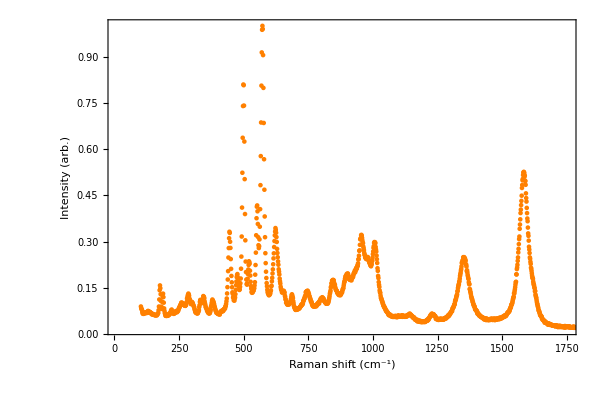

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Raman/RESULTS_Raman/"];
expRaman=ReadList[{"DCmelt011.normalised"}[[1]],{Number,Number,Number}];
expRamanPlot2=Show[{ListPlot[Transpose[{Transpose[expRaman][[1]],Transpose[expRaman][[3]]}],PlotStyle->Orange,PlotRange->{{100,1700},{0,50}},PlotStyle->Dashed]},FrameLabel->{"Raman shift (cm^-1)","Intensity (arb.)"},Frame->True,PlotRange->{{10,1750},All},AspectRatio->0.66,ImageSize->{600,600},PlotLabel->"",LabelStyle->Directive[20,Black],FrameStyle->Directive[Thick,Black]]
```

InterpolatingFunction[{{0., 2002.05}}, <>]

0.0552429-0.0000242901 x

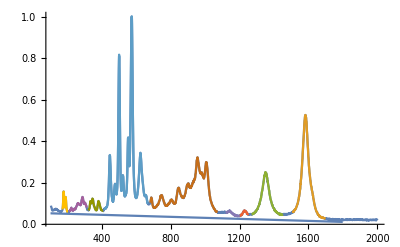

```mathematica
graphite=Transpose[{Transpose[expRaman][[1]],Transpose[expRaman][[3]]}];
graphiteInt=Interpolation[graphite]
graphitePeakA=Table[{x,graphiteInt[x]},{x,1510,1700}];
graphitePeakB=Table[{x,graphiteInt[x]},{x,1270,1450}];
graphitePeakC=Table[{x,graphiteInt[x]},{x,1200,1250}];
graphitePeakD=Table[{x,graphiteInt[x]},{x,1120,1200}];
defectPeakA=Table[{x,graphiteInt[x]},{x,680,1070}];
defectPeakB=Table[{x,graphiteInt[x]},{x,320,405}];
carbonPeakA=Table[{x,graphiteInt[x]},{x,412,666}];
zircPeakA=Table[{x,graphiteInt[x]},{x,170,200}];
zircPeakB=Table[{x,graphiteInt[x]},{x,210,310}];
graphiteP=ListLinePlot[{graphite,graphitePeakA,graphitePeakB,graphitePeakC,graphitePeakD,defectPeakA,carbonPeakA,zircPeakA,zircPeakB,defectPeakB},PlotRange->All];
correction=(graphiteInt[1780]-0.065)/(1780-10)*x-((graphiteInt[1780]-0.065)/(1780-10)*x/.x->10)+0.065-0.01
Show[{graphiteP,Plot[correction,{x,100,1800}]},PlotRange->All]
```

## Main band zirconium states

Set::write: Tag Plus in (c/(b π (1+(Times[«2»]+x)^2/b^2))+f/(e π (1+(Times[«2»]+x)^2/e^2)))[x_] is Protected.

0.0552429-0.0000242901 x+c/(b π (1+(-a+x)^2/b^2))+f/(e π (1+(-d+x)^2/e^2))

FittedModel[0.102443/(1+0.0159412 (-189.27+x)^2)+0.130122/(1+0.0581089 (-175.863+x)^2)]

{a→189.27,b→7.92025,c→2.54902,d→175.863,e→4.14838,f→1.69582}

{{a→189.27,b→7.92025,c→2.54902},{d→175.863,e→4.14838,f→1.69582}}

{189.27,175.863}

{0.0552429+0.102443/(1+0.0159412 (-189.27+x)^2)-0.0000242901 x,0.0552429+0.130122/(1+0.0581089 (-175.863+x)^2)-0.0000242901 x}

{0.153089,0.181093}

{0.101867,0.116032}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{{x→181.32},{x→197.16}},{{x→171.708},{x→180.005}}}

{15.8408,8.29679}

Part::partw: Part 3 of {0.0547667,0.0546191} does not exist.

Part::partw: Part 3 of {0.0545671,0.0544015} does not exist.

Part::partw: Part 4 of {0.0547667,0.0546191} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 9 in {0.0547667,0.0546191}.

Part::take: Cannot take positions 1 through 9 in {0.0545671,0.0544015}.

Part::take: Cannot take positions 1 through 9 in {0.0552429+0.102443/(1+0.0159412 Plus[«2»]^2)-0.0000242901 x,0.0552429+0.130122/(1+0.0581089 Plus[«2»]^2)-0.0000242901 x}.

General::stop: Further output of Part::take will be suppressed during this calculation.

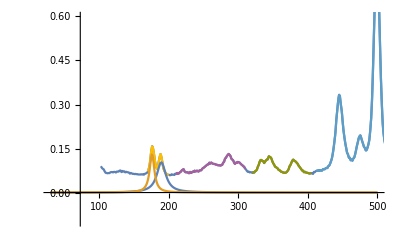

```mathematica
(*carbonPeakA - 2 defects*)
parameterList={a,b,c,d,e,f};
parameterListThrees=Partition[parameterList,3];
ClearAll[model]
model=Sum[(parameterListThrees[[counter]][[3]]*PDF[CauchyDistribution[parameterListThrees[[counter]][[1]],parameterListThrees[[counter]][[2]]],x]),{counter,1,Length@parameterListThrees}];

model[x_]=model+correction
nonlinFitA=NonlinearModelFit[zircPeakA,model,parameterList,x,MaxIterations->10000]


peakAllParamsFlat=nonlinFitA[[1]][[2]]
peakAllParams=Partition[nonlinFitA[[1]][[2]],3]
peakAllFreqZ=Table[peakAllParams[[counter]][[1]][[2]],{counter,1,Length@peakAllParams}]

fitAllZ=Table[(nonlinFitA[[1]][[-1]][[2]][[counter]]+correction),{counter,1,Length@peakAllParams}]/.peakAllParamsFlat
intensityAllZ=Table[fitAllZ[[counter]]/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]],{counter,1,Length@peakAllParams}]
halfIntensityAllZ=Table[intensityAllZ[[counter]]/2+((correction)/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]])/2,{counter,1,Length@peakAllParams}]
widthParamsAllZ=Table[Solve[fitAllZ[[counter]]==halfIntensityAllZ[[counter]],{x}][[2;;3]],{counter,1,Length@peakAllParams}]
FWHMallZ=Table[widthParamsAllZ[[counter]][[2]][[1]][[2]]-widthParamsAllZ[[counter]][[1]][[1]][[2]],{counter,1,Length@peakAllParams}]
Show[{graphiteP,Plot[{Evaluate@Flatten@Table[fitAllZ[[counter]]-correction,{counter,1,9}],Total@fitAllZ[[1;;9]]-9correction},{x,30,500},PlotRange->{{30,500},All}]},PlotRange->{{30,500},{-0.1,0.6}}]
```

189.27 | 0.153089
175.863 | 0.181093

189.27 | 0.101867 | 7.92042
175.863 | 0.116032 | 4.1484

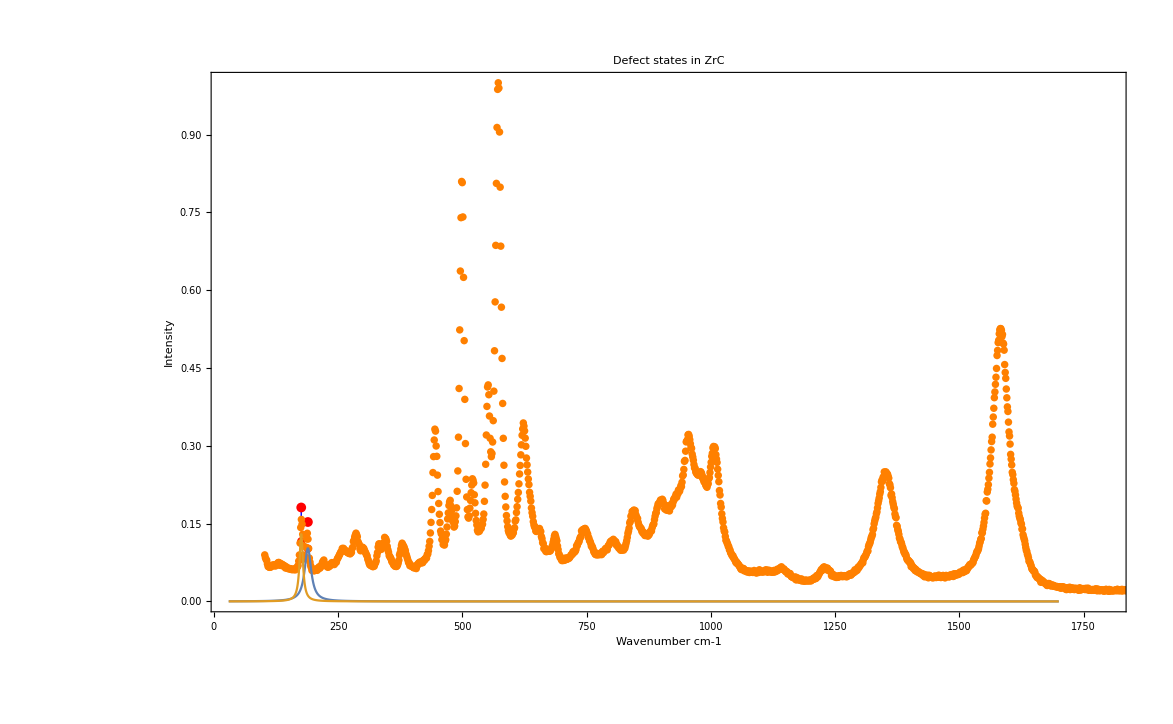

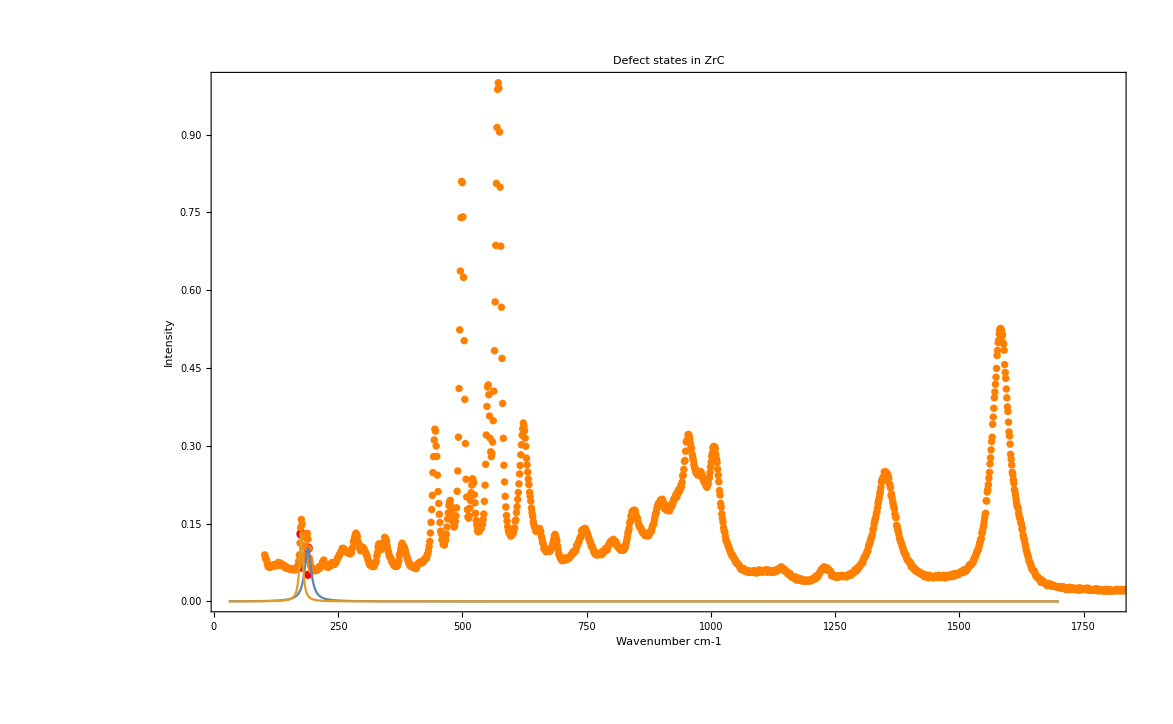

```mathematica
zircMaxPoints=Table[{peakAllFreqZ[[counter]],intensityAllZ[[counter]]},{counter,1,Length@parameterListThrees}];
zircMaxPoints//TableForm
zircWidthPoints=Table[{peakAllFreqZ[[counter]],halfIntensityAllZ[[counter]],FWHMallZ[[counter]]/2},{counter,1,Length@parameterListThrees}];
zircWidthPoints//TableForm

Needs["ErrorBarPlots`"]
f[x_]:={{x[[1]],x[[2]]},ErrorBar[x[[3]],0]}
f2[y_]:={{y[[1]],y[[2]]-correction/.x->y[[1]]},ErrorBar[y[[3]],0]}
f3[y_]:={y[[1]],y[[2]]-correction/.x->y[[1]]}
zircStates=Show[{ListPlot[zircMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{30,1800},All}],ErrorListPlot[f/@zircWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{30,1800},All}],Plot[Evaluate@Flatten@Table[fitAllZ[[counter]]-correction,{counter,1,Length@parameterListThrees}],{x,30,1700},PlotRange->{{30,1800},All}]},PlotRange->{{30,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
zircStates2=Show[{ListPlot[f3/@zircMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{30,1800},All}],ErrorListPlot[f2/@zircWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{30,1800},All}],Plot[Evaluate@Flatten@Table[fitAllZ[[counter]]-correction,{counter,1,Length@parameterListThrees}],{x,30,1700},PlotRange->{{30,1800},All}]},PlotRange->{{30,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

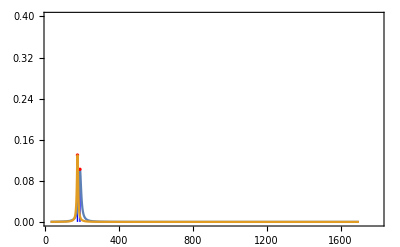

```mathematica
zircOnlyStates2=Show[{ListPlot[f3/@zircMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{30,1800},{0,0.4}}],Plot[Evaluate@Flatten@Table[fitAllZ[[counter]]-correction,{counter,1,Length@parameterListThrees}],{x,30,1700},PlotRange->{{30,1800},All}]}]
```

## SECOND ZIRC BAND

Set::write: Tag Plus in (c/(b π (1+(Times[«2»]+x)^2/b^2))+f/(e π (1+(Times[«2»]+x)^2/e^2))+i/(h π (1+(Times[«2»]+x)^2/h^2))+l/(k π (1+(Times[«2»]+x)^2/k^2)))[x_] is Protected.

0.0552429-0.0000242901 x+c/(b π (1+(-a+x)^2/b^2))+f/(e π (1+(-d+x)^2/e^2))+i/(h π (1+(-g+x)^2/h^2))+l/(k π (1+(-j+x)^2/k^2))

FittedModel[0.072201/(1+0.00477226 (-303.63+x)^2)+0.0678402/(1+0.0184662 («1»)^2)+0.0737669/(1+«22» («1»)^2)+0.0556305/(1+0.00174963 (-217.821+x)^2)]

{a→285.592,b→7.35888,c→1.56837,d→260.564,e→19.9167,f→4.6156,g→303.63,h→14.4756,i→3.28346,j→217.821,k→23.9071,l→4.1782}

{{a→285.592,b→7.35888,c→1.56837},{d→260.564,e→19.9167,f→4.6156},{g→303.63,h→14.4756,i→3.28346},{j→217.821,k→23.9071,l→4.1782}}

{285.592,260.564,303.63,217.821}

{0.0552429+0.0678402/(1+0.0184662 (-285.592+x)^2)-0.0000242901 x,0.0552429+0.0737669/(1+0.00252096 (-260.564+x)^2)-0.0000242901 x,0.0552429+0.072201/(1+0.00477226 (-303.63+x)^2)-0.0000242901 x,0.0552429+0.0556305/(1+0.00174963 (-217.821+x)^2)-0.0000242901 x}

{0.116146,0.122681,0.120069,0.105582}

{0.0822259,0.0857972,0.0839682,0.0777672}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{x→278.194},{x→292.913}},{{x→240.38},{x→280.224}},{{x→289.011},{x→317.967}},{{x→193.399},{x→241.244}}}

{14.7184,39.8437,28.9554,47.8455}

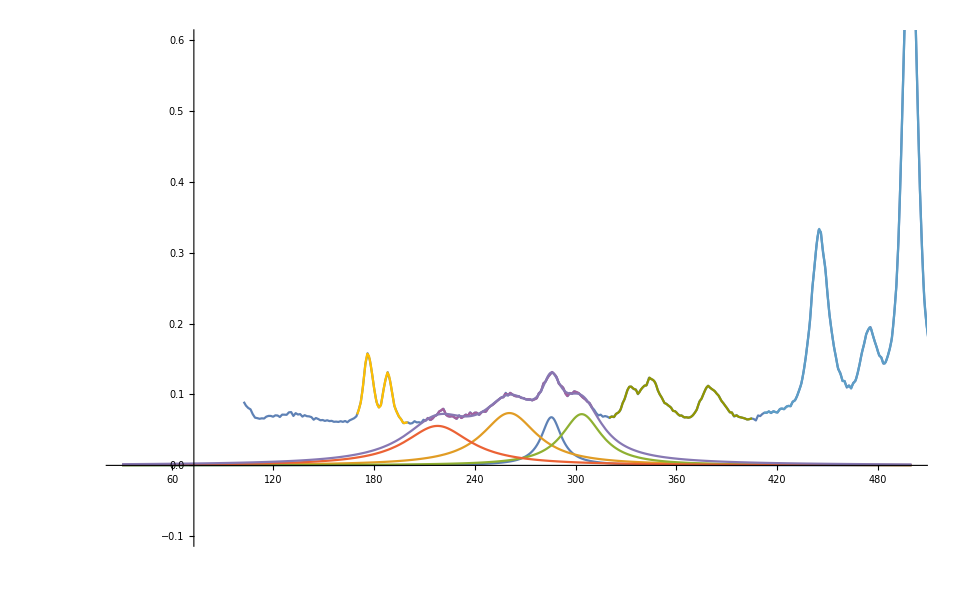

```mathematica
(*carbonPeakA - 2 defects*)
parameterList={a,b,c,d,e,f,g,h,i,j,k,l};
parameterListThrees=Partition[parameterList,3];
ClearAll[model]
model=Sum[(parameterListThrees[[counter]][[3]]*PDF[CauchyDistribution[parameterListThrees[[counter]][[1]],parameterListThrees[[counter]][[2]]],x]),{counter,1,Length@parameterListThrees}];

model[x_]=model+correction
nonlinFitA=NonlinearModelFit[zircPeakB,model,parameterList,x,MaxIterations->10000]


peakAllParamsFlat=nonlinFitA[[1]][[2]]
peakAllParams=Partition[nonlinFitA[[1]][[2]],3]
peakAllFreqZb=Table[peakAllParams[[counter]][[1]][[2]],{counter,1,Length@peakAllParams}]

fitAllZb=Table[(nonlinFitA[[1]][[-1]][[2]][[counter]]+correction),{counter,1,Length@peakAllParams}]/.peakAllParamsFlat
intensityAllZb=Table[fitAllZb[[counter]]/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]],{counter,1,Length@peakAllParams}]
halfIntensityAllZb=Table[intensityAllZb[[counter]]/2+((correction)/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]])/2,{counter,1,Length@peakAllParams}]
widthParamsAllZb=Table[Solve[fitAllZb[[counter]]==halfIntensityAllZb[[counter]],{x}][[2;;3]],{counter,1,Length@peakAllParams}]
FWHMallZb=Table[widthParamsAllZb[[counter]][[2]][[1]][[2]]-widthParamsAllZb[[counter]][[1]][[1]][[2]],{counter,1,Length@peakAllParams}]
len=Length@peakAllParams;
Show[{graphiteP,Plot[{Evaluate@Flatten@Table[fitAllZb[[counter]]-correction,{counter,1,len}],Total@fitAllZb[[1;;len]]-len*correction},{x,30,500},PlotRange->{{30,500},All}]},PlotRange->{{30,500},{-0.1,0.6}}]
```

285.592 | 0.116146
260.564 | 0.122681
303.63 | 0.120069
217.821 | 0.105582

285.592 | 0.0822259 | 7.35919
260.564 | 0.0857972 | 19.9218
303.63 | 0.0839682 | 14.4777
217.821 | 0.0777672 | 23.9227

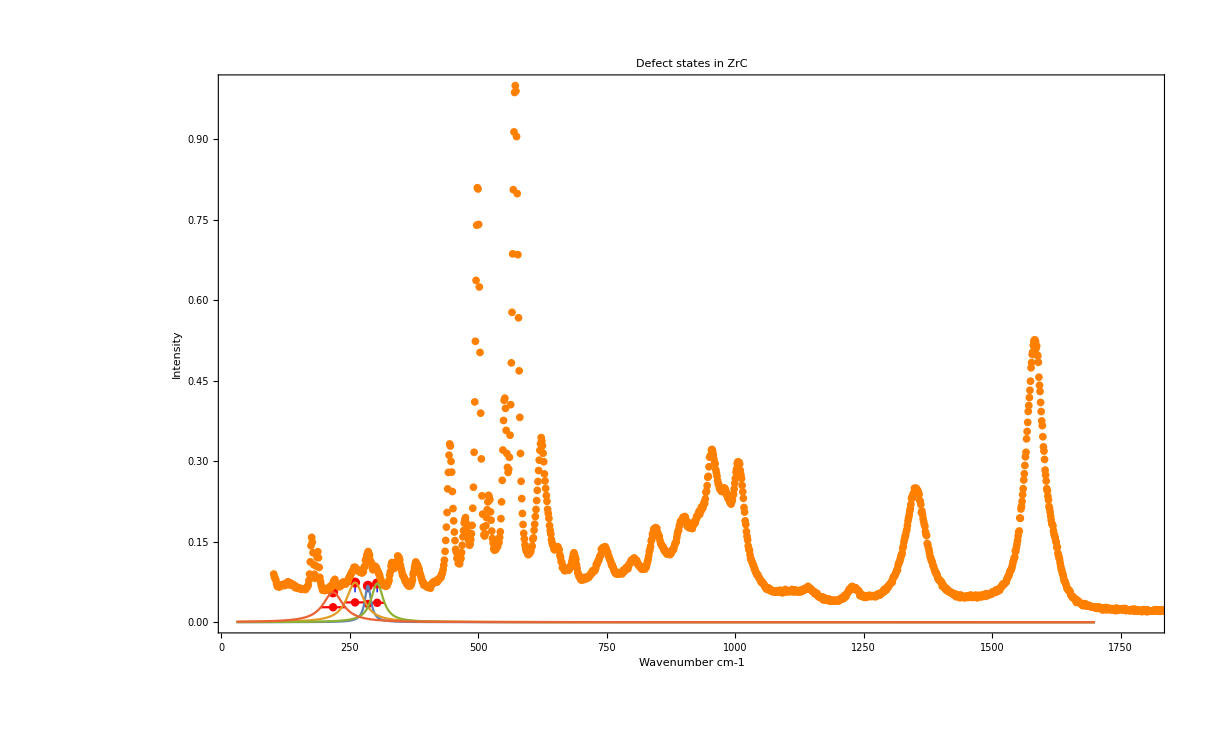

```mathematica
zircBMaxPoints=Table[{peakAllFreqZb[[counter]],intensityAllZb[[counter]]},{counter,1,Length@parameterListThrees}];
zircBMaxPoints//TableForm
zircBWidthPoints=Table[{peakAllFreqZb[[counter]],halfIntensityAllZb[[counter]],FWHMallZb[[counter]]/2},{counter,1,Length@parameterListThrees}];
zircBWidthPoints//TableForm


zircBStates=Show[{ListPlot[zircBMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{30,1800},All}],ErrorListPlot[f/@zircBWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{30,1800},All}],Plot[Evaluate@Flatten@Table[fitAllZb[[counter]]-correction,{counter,1,Length@parameterListThrees}],{x,30,1700},PlotRange->{{30,1800},All}]},PlotRange->{{30,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}];

zircBStates2=Show[{ListPlot[f3/@zircBMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{30,1800},All}],ErrorListPlot[f2/@zircBWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{30,1800},All}],Plot[Evaluate@Flatten@Table[fitAllZb[[counter]]-correction,{counter,1,Length@parameterListThrees}],{x,30,1700},PlotRange->{{30,1800},All}]},PlotRange->{{30,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

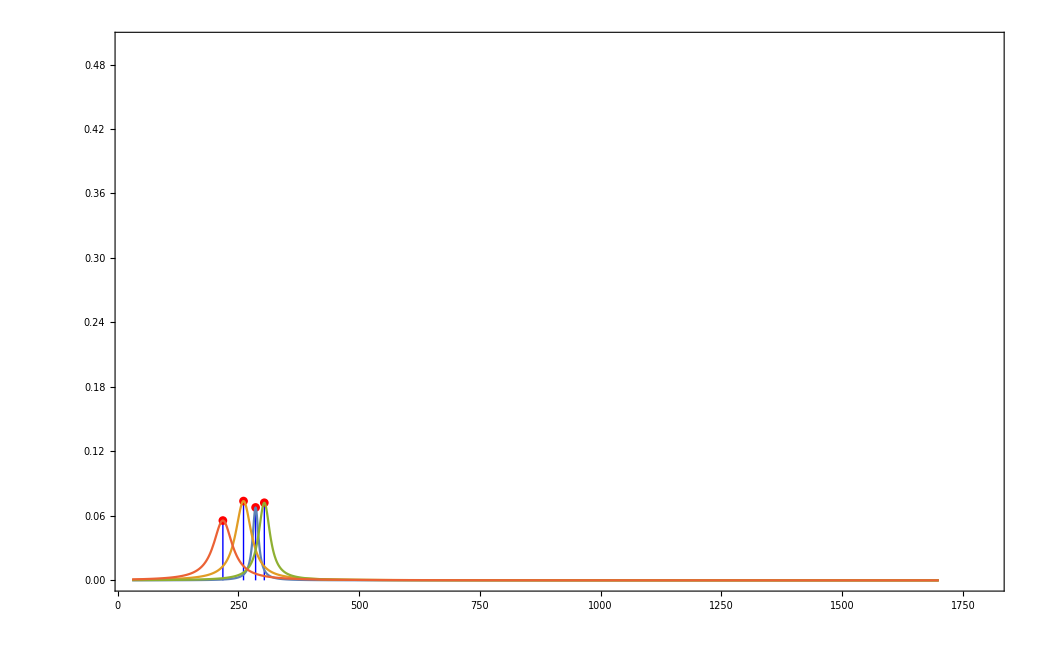

```mathematica
zircOnlyBStates2=Show[{ListPlot[f3/@zircBMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{30,1800},{0,0.5}}],Plot[Evaluate@Flatten@Table[fitAllZb[[counter]]-correction,{counter,1,Length@fitAllZb}],{x,30,1700},PlotRange->{{30,1800},{0,0.5}}]}]
```

## Carbon main band states

```mathematica
(*carbonPeakA - 7 defects*)
parameterList={a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,xx,y,α,β,γ};
parameterListThrees=Partition[parameterList,3];
ClearAll[model]
model=Sum[(parameterListThrees[[counter]][[3]]*PDF[CauchyDistribution[parameterListThrees[[counter]][[1]],parameterListThrees[[counter]][[2]]],x]),{counter,1,Length@parameterListThrees}];

model[x_]=model+correction
nonlinFitA=NonlinearModelFit[carbonPeakA,model,parameterList,x,MaxIterations->10000]
```

Set::write: Tag Plus in (c/(b π (1+(Times[«2»]+x)^2/b^2))+f/(e π (1+(Times[«2»]+x)^2/e^2))+i/(h π (1+(Times[«2»]+x)^2/h^2))+l/(k π (1+(Times[«2»]+x)^2/k^2))+o/(n π (1+(Times[«2»]+x)^2/n^2))+r/(π q (1+(Times[«2»]+x)^2/q^2))+u/(π t (1+(Times[«2»]+x)^2/t^2))+y/(π (1+(Times[«2»]+x)^2/xx^2) xx)+γ/(π (1+(x+Times[«2»])^2/β^2) β))[x_] is Protected.

0.0552429-0.0000242901 x+c/(b π (1+(-a+x)^2/b^2))+f/(e π (1+(-d+x)^2/e^2))+i/(h π (1+(-g+x)^2/h^2))+l/(k π (1+(-j+x)^2/k^2))+o/(n π (1+(-m+x)^2/n^2))+r/(π q (1+(-p+x)^2/q^2))+u/(π t (1+(-s+x)^2/t^2))+y/(π (1+(-v+x)^2/xx^2) xx)+γ/(π (1+(x-α)^2/β^2) β)

FittedModel[0.0910018/(1+0.00254567 (-655.39+x)^2)+«7»+0.0511756/(1+0.0054311 (-415.044+x)^2)]

{a→522.199,b→6.80103,c→3.41704,d→445.422,e→7.2675,f→6.82695,g→623.297,h→11.8034,i→10.869,j→572.301,k→6.45998,l→20.1065,m→655.39,n→19.8198,o→5.6663,p→415.044,q→13.5693,r→2.18157,s→551.087,t→4.87033,u→4.68271,v→474.293,xx→6.85986,y→2.81452,α→499.096,β→4.99322,γ→12.4993}

{{a→522.199,b→6.80103,c→3.41704},{d→445.422,e→7.2675,f→6.82695},{g→623.297,h→11.8034,i→10.869},{j→572.301,k→6.45998,l→20.1065},{m→655.39,n→19.8198,o→5.6663},{p→415.044,q→13.5693,r→2.18157},{s→551.087,t→4.87033,u→4.68271},{v→474.293,xx→6.85986,y→2.81452},{α→499.096,β→4.99322,γ→12.4993}}

{522.199,445.422,623.297,572.301,655.39,415.044,551.087,474.293,499.096}

{0.0552429+0.159928/(1+0.0216197 (-522.199+x)^2)-0.0000242901 x,0.0552429+0.299014/(1+0.0189335 (-445.422+x)^2)-0.0000242901 x,0.0552429+0.293112/(1+0.00717774 (-623.297+x)^2)-0.0000242901 x,0.0552429+0.990731/(1+0.0239628 (-572.301+x)^2)-0.0000242901 x,0.0552429+0.0910018/(1+0.00254567 (-655.39+x)^2)-0.0000242901 x,0.0552429+0.0511756/(1+0.0054311 (-415.044+x)^2)-0.0000242901 x,0.0552429+0.306048/(1+0.0421582 (-551.087+x)^2)-0.0000242901 x,0.0552429+0.130599/(1+0.0212505 (-474.293+x)^2)-0.0000242901 x,0.0552429+0.796811/(1+0.0401087 (-499.096+x)^2)-0.0000242901 x}

{0.202487,0.343438,0.333215,1.03207,0.130325,0.0963371,0.347905,0.174321,0.839931}

{0.122523,0.193931,0.186659,0.536707,0.0848243,0.0707493,0.194881,0.109022,0.441525}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{x→515.384},{x→528.987}},{{x→438.146},{x→452.681}},{{x→611.47},{x→635.077}},{{x→565.839},{x→578.759}},{{x→635.357},{x→675.004}},{{x→401.296},{x→428.442}},{{x→546.213},{x→555.953}},{{x→467.415},{x→481.135}},{{x→494.101},{x→504.087}}}

{13.6022,14.535,23.6069,12.92,39.6463,27.1453,9.74068,13.7198,9.98644}

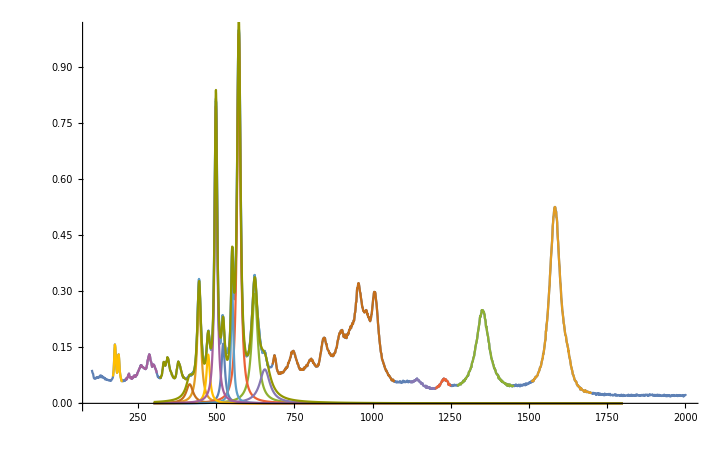

```mathematica
peakAllParamsFlat=nonlinFitA[[1]][[2]]
peakAllParams=Partition[nonlinFitA[[1]][[2]],3]
peakAllFreqC=Table[peakAllParams[[counter]][[1]][[2]],{counter,1,Length@peakAllParams}]

fitAllC=Table[(nonlinFitA[[1]][[-1]][[2]][[counter]]+correction),{counter,1,Length@peakAllParams}]/.peakAllParamsFlat
intensityAllC=Table[fitAllC[[counter]]/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]],{counter,1,Length@peakAllParams}]
halfIntensityAllC=Table[intensityAllC[[counter]]/2+((correction)/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]])/2,{counter,1,Length@peakAllParams}]
widthParamsAllC=Table[Solve[fitAllC[[counter]]==halfIntensityAllC[[counter]],{x}][[2;;3]],{counter,1,Length@peakAllParams}]
FWHMallC=Table[widthParamsAllC[[counter]][[2]][[1]][[2]]-widthParamsAllC[[counter]][[1]][[1]][[2]],{counter,1,Length@peakAllParams}]
Show[{graphiteP,Plot[{Evaluate@Flatten@Table[fitAllC[[counter]]-correction,{counter,1,9}],Total@fitAllC[[1;;9]]-9correction},{x,300,1800},PlotRange->All]}]
```

522.199 | 0.202487
445.422 | 0.343438
623.297 | 0.333215
572.301 | 1.03207
655.39 | 0.130325
415.044 | 0.0963371
551.087 | 0.347905
474.293 | 0.174321
499.096 | 0.839931

522.199 | 0.122523 | 6.80108
445.422 | 0.193931 | 7.26751
623.297 | 0.186659 | 11.8034
572.301 | 0.536707 | 6.45998
655.39 | 0.0848243 | 19.8231
415.044 | 0.0707493 | 13.5726
551.087 | 0.194881 | 4.87034
474.293 | 0.109022 | 6.85992
499.096 | 0.441525 | 4.99322

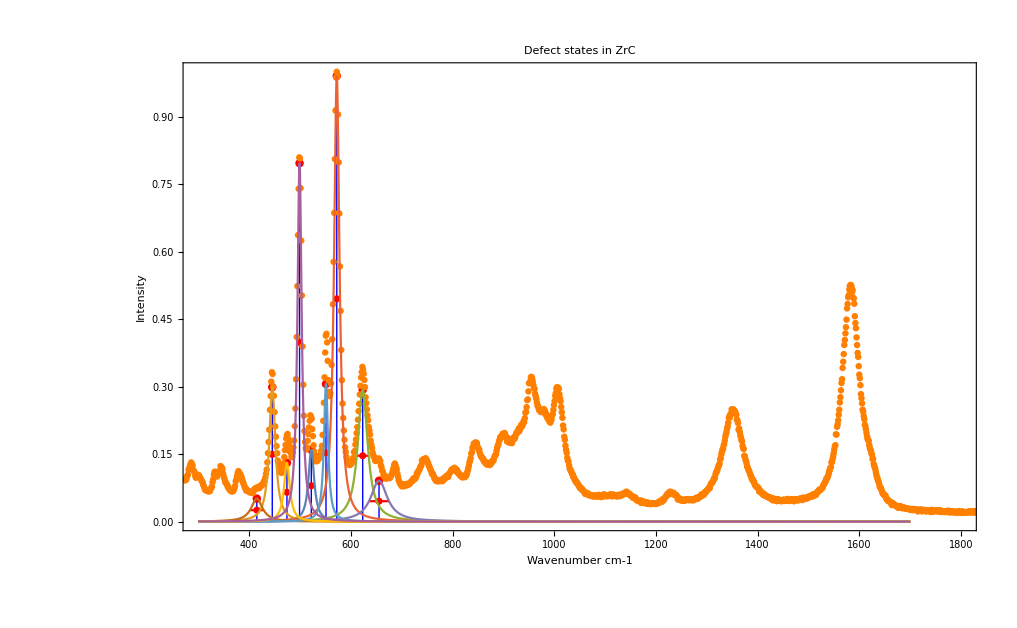

```mathematica
carbonMaxPoints=Table[{peakAllFreqC[[counter]],intensityAllC[[counter]]},{counter,1,Length@parameterListThrees}];
carbonMaxPoints//TableForm
carbonWidthPoints=Table[{peakAllFreqC[[counter]],halfIntensityAllC[[counter]],FWHMallC[[counter]]/2},{counter,1,Length@parameterListThrees}];
carbonWidthPoints//TableForm


carbonStates=Show[{ListPlot[carbonMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],ErrorListPlot[f/@carbonWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAllC[[counter]]-correction,{counter,1,Length@parameterListThrees}],{x,300,1700},PlotRange->{{1000,1800},All}]},PlotRange->{{300,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}];
carbonStates2=Show[{ListPlot[f3/@carbonMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],ErrorListPlot[f2/@carbonWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAllC[[counter]]-correction,{counter,1,Length@parameterListThrees}],{x,300,1700},PlotRange->{{1000,1800},All}]},PlotRange->{{300,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

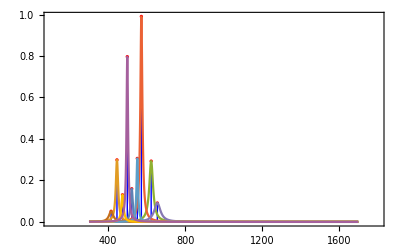

```mathematica
carbonOnlyStates2=Show[{ListPlot[f3/@carbonMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{100,1800},All}],Plot[Evaluate@Flatten@Table[fitAllC[[counter]]-correction,{counter,1,Length@fitAllC}],{x,300,1700},PlotRange->{{100,1800},All}]}]
```

## Defects states

Set::write: Tag Plus in (c/(b π (1+(Times[«2»]+x)^2/b^2))+f/(e π (1+(Times[«2»]+x)^2/e^2))+i/(h π (1+(Times[«2»]+x)^2/h^2))+l/(k π (1+(Times[«2»]+x)^2/k^2))+o/(n π (1+(Times[«2»]+x)^2/n^2))+r/(π q (1+(Times[«2»]+x)^2/q^2))+u/(π t (1+(Times[«2»]+x)^2/t^2))+y/(π (1+(Times[«2»]+x)^2/xx^2) xx)+γ/(π (1+(x+Times[«2»])^2/β^2) β)+ϵ/(π (1+(x+Times[«2»])^2/μ^2) μ))[x_] is Protected.

0.0552429-0.0000242901 x+c/(b π (1+(-a+x)^2/b^2))+f/(e π (1+(-d+x)^2/e^2))+i/(h π (1+(-g+x)^2/h^2))+l/(k π (1+(-j+x)^2/k^2))+o/(n π (1+(-m+x)^2/n^2))+r/(π q (1+(-p+x)^2/q^2))+u/(π t (1+(-s+x)^2/t^2))+y/(π (1+(-v+x)^2/xx^2) xx)+γ/(π (1+(x-α)^2/β^2) β)+ϵ/(π (1+(x-δ)^2/μ^2) μ)

FittedModel[0.184905/(1+0.00700612 (-1007.84+x)^2)+«8»+0.0790631/(1+0.0144131 (-685.645+x)^2)]

{a→735.606,b→51.3526,c→9.58328,d→943.707,e→78.0899,f→40.6106,g→800.764,h→13.9102,i→1.97991,j→845.016,k→12.5118,l→3.66342,m→979.682,n→10.6486,o→1.89313,p→745.905,q→12.353,r→2.1247,s→685.645,t→8.32955,u→2.06893,v→1007.84,xx→11.9471,y→6.94001,α→955.386,β→10.6183,γ→4.4893,δ→896.802,μ→10.7276,ϵ→1.7804}

{{a→735.606,b→51.3526,c→9.58328},{d→943.707,e→78.0899,f→40.6106},{g→800.764,h→13.9102,i→1.97991},{j→845.016,k→12.5118,l→3.66342},{m→979.682,n→10.6486,o→1.89313},{p→745.905,q→12.353,r→2.1247},{s→685.645,t→8.32955,u→2.06893},{v→1007.84,xx→11.9471,y→6.94001},{α→955.386,β→10.6183,γ→4.4893},{δ→896.802,μ→10.7276,ϵ→1.7804}}

{735.606,943.707,800.764,845.016,979.682,745.905,685.645,1007.84,955.386,896.802}

{0.0552429+0.0594021/(1+0.000379206 (-735.606+x)^2)-0.0000242901 x,0.0552429+0.165537/(1+0.000163987 (-943.707+x)^2)-0.0000242901 x,0.0552429+0.0453068/(1+0.00516815 (-800.764+x)^2)-0.0000242901 x,0.0552429+0.0932004/(1+0.00638794 (-845.016+x)^2)-0.0000242901 x,0.0552429+0.0565899/(1+0.00881898 (-979.682+x)^2)-0.0000242901 x,0.0552429+0.0547491/(1+0.00655324 (-745.905+x)^2)-0.0000242901 x,0.0552429+0.0790631/(1+0.0144131 (-685.645+x)^2)-0.0000242901 x,0.0552429+0.184905/(1+0.00700612 (-1007.84+x)^2)-0.0000242901 x,0.0552429+0.134578/(1+0.00886937 (-955.386+x)^2)-0.0000242901 x,0.0552429+0.0528285/(1+0.00868958 (-896.802+x)^2)-0.0000242901 x}

{0.0967771,0.197857,0.081099,0.127918,0.0880362,0.0918739,0.117652,0.215667,0.166615,0.086288}

{0.067076,0.115089,0.0584456,0.0813176,0.0597413,0.0644993,0.07812,0.123215,0.0993256,0.0598737}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{x→681.949},{x→784.928}},{{x→863.763},{x→1020.07}},{{x→786.642},{x→814.472}},{{x→832.422},{x→857.447}},{{x→968.935},{x→990.234}},{{x→733.415},{x→758.125}},{{x→677.273},{x→693.933}},{{x→995.859},{x→1019.75}},{{x→944.727},{x→965.964}},{{x→885.967},{x→907.425}}}

{102.979,156.303,27.8296,25.0252,21.2998,24.7104,16.6598,23.8945,21.237,21.4582}

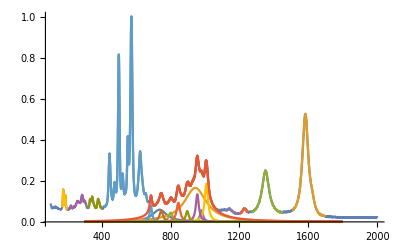

```mathematica
(*DefectPeakA - 7 defects*)
parameterList={a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,xx,y,α,β,γ,δ,μ,ϵ};
parameterListThrees=Partition[parameterList,3];
ClearAll[model]
model=Sum[(parameterListThrees[[counter]][[3]]*PDF[CauchyDistribution[parameterListThrees[[counter]][[1]],parameterListThrees[[counter]][[2]]],x]),{counter,1,Length@parameterListThrees}];

model[x_]=model+correction
nonlinFitA=NonlinearModelFit[defectPeakA,model,parameterList,x,MaxIterations->10000]

peakAllParamsFlat=nonlinFitA[[1]][[2]]
peakAllParams=Partition[nonlinFitA[[1]][[2]],3]
peakAllFreq=Table[peakAllParams[[counter]][[1]][[2]],{counter,1,Length@peakAllParams}]

fitAll=Table[(nonlinFitA[[1]][[-1]][[2]][[counter]]+correction),{counter,1,Length@peakAllParams}]/.peakAllParamsFlat
intensityAll=Table[fitAll[[counter]]/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]],{counter,1,Length@peakAllParams}]
halfIntensityAll=Table[intensityAll[[counter]]/2+((correction)/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]])/2,{counter,1,Length@peakAllParams}]
widthParamsAll=Table[Solve[fitAll[[counter]]==halfIntensityAll[[counter]],{x}][[2;;3]],{counter,1,Length@peakAllParams}]
FWHMall=Table[widthParamsAll[[counter]][[2]][[1]][[2]]-widthParamsAll[[counter]][[1]][[1]][[2]],{counter,1,Length@peakAllParams}]
Show[{graphiteP,Plot[{Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,10}],Total@fitAll[[1;;10]]-10correction},{x,300,1800},PlotRange->All]}]
```

```mathematica
defectMaxPoints=Table[{peakAllFreq[[counter]],intensityAll[[counter]]},{counter,1,Length@parameterListThrees}];
defectMaxPoints//TableForm
defectWidthPoints=Table[{peakAllFreq[[counter]],halfIntensityAll[[counter]],FWHMall[[counter]]/2},{counter,1,Length@parameterListThrees}];
defectWidthPoints//TableForm
```

735.606 | 0.0967771
943.707 | 0.197857
800.764 | 0.081099
845.016 | 0.127918
979.682 | 0.0880362
745.905 | 0.0918739
685.645 | 0.117652
1007.84 | 0.215667
955.386 | 0.166615
896.802 | 0.086288

735.606 | 0.067076 | 51.4896
943.707 | 0.115089 | 78.1516
800.764 | 0.0584456 | 13.9148
845.016 | 0.0813176 | 12.5126
979.682 | 0.0597413 | 10.6499
745.905 | 0.0644993 | 12.3552
685.645 | 0.07812 | 8.32988
1007.84 | 0.123215 | 11.9472
955.386 | 0.0993256 | 10.6185
896.802 | 0.0598737 | 10.7291

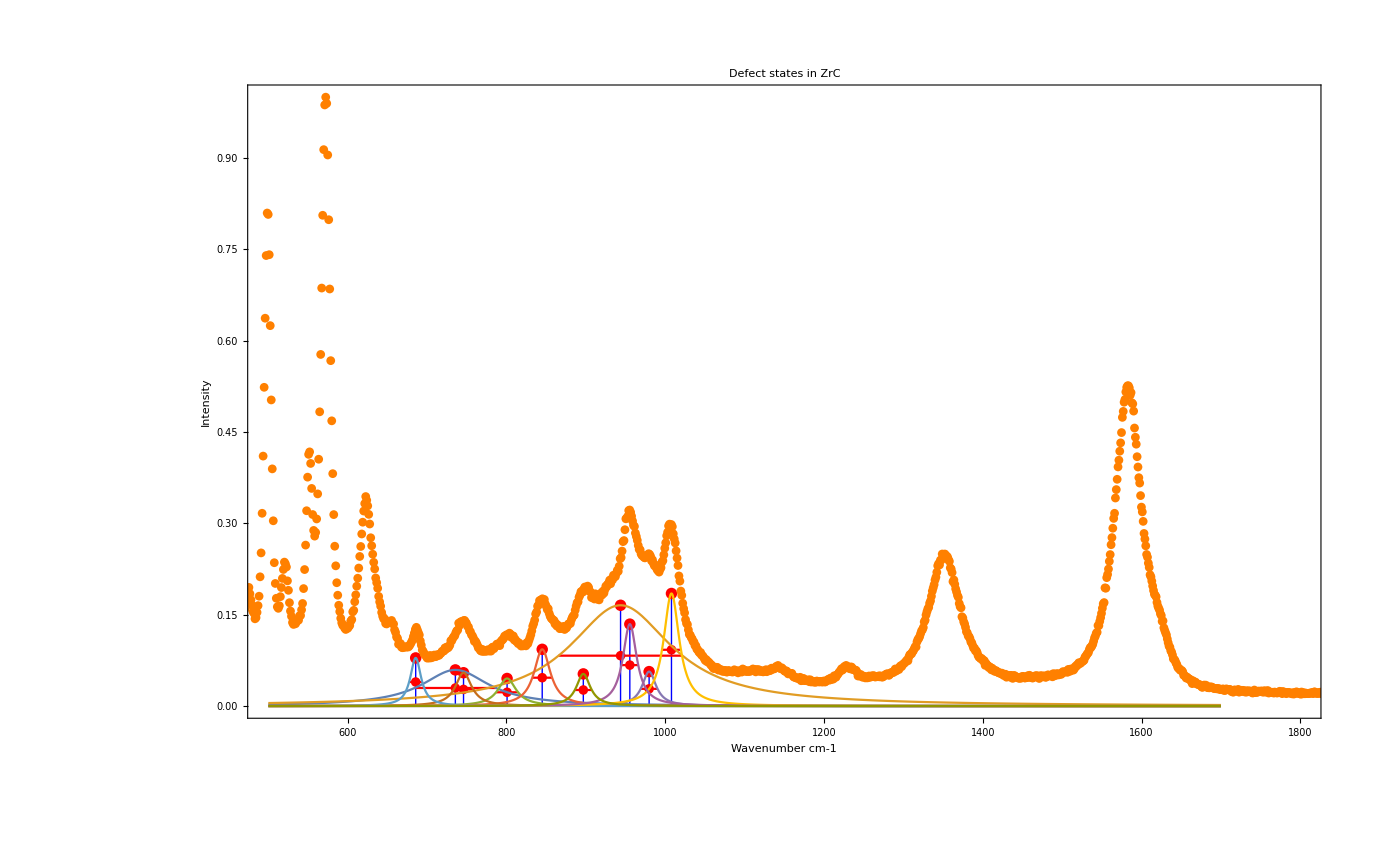

```mathematica
defectStates=Show[{ListPlot[defectMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],ErrorListPlot[f/@defectWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,10}],{x,500,1700},PlotRange->{{1000,1800},All}]},PlotRange->{{500,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}];
defectStates2=Show[{ListPlot[f3/@defectMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],ErrorListPlot[f2/@defectWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,10}],{x,500,1700},PlotRange->{{1000,1800},All}]},PlotRange->{{500,1800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

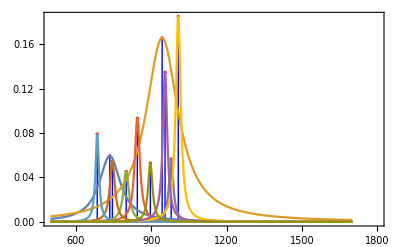

```mathematica
defectOnlyStates2=Show[{ListPlot[f3/@defectMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,10}],{x,500,1700},PlotRange->{{1000,1800},All}]}]
```

```mathematica
ClearAll[a]
```

## Defect states lower

```mathematica
a
```

a

```mathematica
ClearAll[model]
ClearAll@@{a,b,c,d,e,f,g,h,i}
```

Set::write: Tag Plus in (c/(b π (1+(Times[«2»]+x)^2/b^2))+f/(e π (1+(Times[«2»]+x)^2/e^2))+i/(h π (1+(Times[«2»]+x)^2/h^2)))[x_] is Protected.

0.0552429-0.0000242901 x+c/(b π (1+(-a+x)^2/b^2))+f/(e π (1+(-d+x)^2/e^2))+i/(h π (1+(-g+x)^2/h^2))

FittedModel[0.0460989/(1+0.00313151 (-401.938+x)^2)+0.0699032/(1+0.0148697 (-«19»+x)^2)+0.110664/(1+0.00226064 (-340.083+x)^2)]

{a→380.45,b→8.20067,c→1.80093,d→401.938,e→17.8699,f→2.588,g→340.083,h→21.0322,i→7.3121}

{{a→380.45,b→8.20067,c→1.80093},{d→401.938,e→17.8699,f→2.588},{g→340.083,h→21.0322,i→7.3121}}

{380.45,401.938,340.083}

{0.0552429+0.0699032/(1+0.0148697 (-380.45+x)^2)-0.0000242901 x,0.0552429+0.0460989/(1+0.00313151 (-401.938+x)^2)-0.0000242901 x,0.0552429+0.110664/(1+0.00226064 (-340.083+x)^2)-0.0000242901 x}

{0.115905,0.0915787,0.157647}

{0.0809533,0.0685293,0.102314}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{x→372.202},{x→388.604}},{{x→383.722},{x→419.481}},{{x→318.854},{x→360.924}}}

{16.4021,35.7589,42.0698}

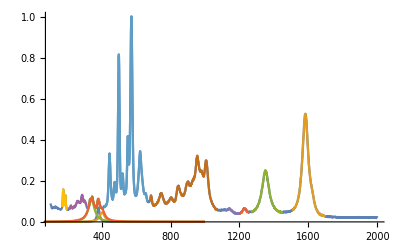

```mathematica
(*DefectPeakA - 7 defects*)
parameterList={a,b,c,d,e,f,g,h,i};
parameterListThrees=Partition[parameterList,3];
ClearAll[model]
ClearAll@x
model=Sum[(parameterListThrees[[counter]][[3]]*PDF[CauchyDistribution[parameterListThrees[[counter]][[1]],parameterListThrees[[counter]][[2]]],x]),{counter,1,Length@parameterListThrees}];

model[x_]=model+correction
nonlinFitA=NonlinearModelFit[defectPeakB,model,parameterList,x,MaxIterations->10000]

peakAllParamsFlat=nonlinFitA[[1]][[2]]
peakAllParams=Partition[nonlinFitA[[1]][[2]],3]
peakAllFreq=Table[peakAllParams[[counter]][[1]][[2]],{counter,1,Length@peakAllParams}]

fitAll=Table[(nonlinFitA[[1]][[-1]][[2]][[counter]]+correction),{counter,1,Length@peakAllParams}]/.peakAllParamsFlat
intensityAll=Table[fitAll[[counter]]/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]],{counter,1,Length@fitAll}]
halfIntensityAll=Table[intensityAll[[counter]]/2+((correction)/.x->parameterListThrees[[counter]][[1]]/.peakAllParams[[counter]])/2,{counter,1,Length@intensityAll}]
widthParamsAll=Table[Solve[fitAll[[counter]]==halfIntensityAll[[counter]],{x}][[2;;3]],{counter,1,Length@fitAll}]
FWHMall=Table[widthParamsAll[[counter]][[2]][[1]][[2]]-widthParamsAll[[counter]][[1]][[1]][[2]],{counter,1,Length@widthParamsAll}]

len=Length@peakAllParams;
Show[{graphiteP,Plot[{Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,len}],Total@fitAll[[1;;len]]-len*correction},{x,30,1000},PlotRange->All]}]
```

380.45 | 0.115905
401.938 | 0.0915787
340.083 | 0.157647

380.45 | 0.0809533 | 8.20107
401.938 | 0.0685293 | 17.8795
340.083 | 0.102314 | 21.0349

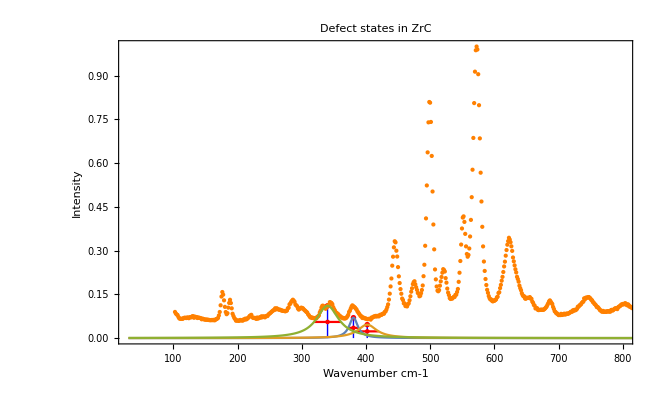

```mathematica
defectBMaxPoints=Table[{peakAllFreq[[counter]],intensityAll[[counter]]},{counter,1,Length@parameterListThrees}];
defectBMaxPoints//TableForm
defectBWidthPoints=Table[{peakAllFreq[[counter]],halfIntensityAll[[counter]],FWHMall[[counter]]/2},{counter,1,Length@parameterListThrees}];
defectBWidthPoints//TableForm


defectStatesB=Show[{ListPlot[defectBMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],ErrorListPlot[f/@defectBWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,Length@fitAll}],{x,30,1700},PlotRange->{{30,1800},All}]},PlotRange->{{30,800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}];


defectStatesB2=Show[{ListPlot[f3/@defectBMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],ErrorListPlot[f2/@defectBWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,Length@fitAll}],{x,30,1700},PlotRange->{{30,1800},All}]},PlotRange->{{30,800},All},PlotLabel->"Defect states in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

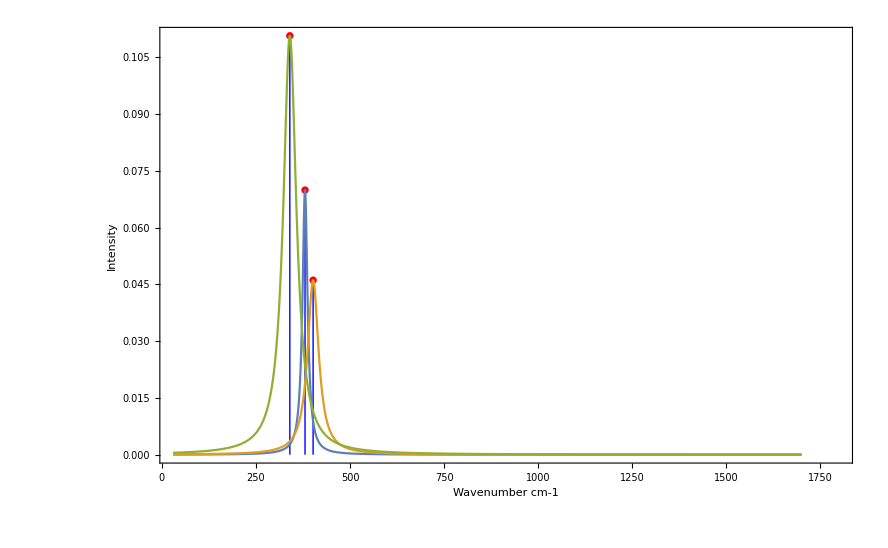

```mathematica
defectOnlyStatesB2=Show[{ListPlot[f3/@defectBMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{500,1800},All}],Plot[Evaluate@Flatten@Table[fitAll[[counter]]-correction,{counter,1,Length@fitAll}],{x,30,1700},PlotRange->{{30,1800},All}]},PlotRange->{{30,1800},All},FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

## Graphite

```mathematica
(*GraphitePeakA*)
ClearAll[model]
model[x_]=c*PDF[CauchyDistribution[a,b],x]+g*PDF[CauchyDistribution[d,e],x]+correction
nonlinFitA=NonlinearModelFit[graphitePeakA,model[x],{a,b,c,d,e,g},x,MaxIterations->10000]
peakOneParams=nonlinFitA[[1]][[2]][[1;;3]]
peakTwoParams=nonlinFitA[[1]][[2]][[4;;6]]
peakOneFreq=peakOneParams[[1]][[2]]
peakTwoFreq=peakTwoParams[[1]][[2]]
fitOne=(nonlinFitA[[1]][[-1]][[2]][[3]]+correction)/.peakOneParams
fitTwo=(nonlinFitA[[1]][[-1]][[2]][[4]]+correction)/.peakTwoParams
intensityOne=fitOne/.x->a/.peakOneParams
intensityTwo=fitTwo/.x->d/.peakTwoParams
(*halfIntensity defined as the intensity half plus half the baseline*)
halfIntensityOne=intensityOne/2+((correction)/.x->a/.peakOneParams)/2
halfIntensityTwo=intensityTwo/2+((correction)/.x->d/.peakTwoParams)/2
widthParamsOne=Solve[fitOne==halfIntensityOne,{x}][[2;;3]]
widthParamsTwo=Solve[fitTwo==halfIntensityTwo,{x}][[2;;3]]
FWHMone=widthParamsOne[[2]][[1]][[2]]-widthParamsOne[[1]][[1]][[2]]
FWHMtwo=widthParamsTwo[[2]][[1]][[2]]-widthParamsTwo[[1]][[1]][[2]]
```

0.0552429-0.0000242901 x+c/(b π (1+(-a+x)^2/b^2))+g/(e π (1+(-d+x)^2/e^2))

FittedModel[0.0552429+0.0372907/(1+0.00899773 (-1620.51+x)^2)+0.50879/(1+0.00240842 (-«19»+x)^2)-0.0000242901 x]

{a→1583.07,b→20.3767,c→32.5703}

{d→1620.51,e→10.5423,g→1.23505}

1583.07

1620.51

0.0552429+0.50879/(1+0.00240842 (-1583.07+x)^2)-0.0000242901 x

0.0552429+0.0372907/(1+0.00899773 (-1620.51+x)^2)-0.0000242901 x

0.52558

0.0531712

0.271185

0.0345258

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1562.65},{x→1603.41}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1609.82},{x→1630.91}}

40.7536

21.0905

```mathematica
(*PeakB*)
model[x_]:=c*PDF[CauchyDistribution[a,b],x]+correction
nonlinFitB=NonlinearModelFit[graphitePeakB,model[x],{a,b,c},x,MaxIterations->10000]
peakOneParamsB=nonlinFitB[[1]][[2]][[1;;3]]
peakOneFreqB=peakOneParamsB[[1]][[2]]
nonlinFitB[[1]][[-1]][[2]][[3]]
fitOneB=(nonlinFitB[[1]][[-1]][[2]][[3]]+correction)/.peakOneParamsB
intensityOneB=fitOneB/.x->a/.peakOneParamsB
(*halfIntensity defined as the intensity half plus half the baseline*)
halfIntensityOneB=intensityOneB/2+((correction)/.x->a/.peakOneParamsB)/2
widthParamsOneB=Solve[fitOneB==halfIntensityOneB,{x}][[2;;3]]
FWHMoneB=widthParamsOneB[[2]][[1]][[2]]-widthParamsOneB[[1]][[1]][[2]]
```

FittedModel[0.0552429+0.222984/(1+0.00142573 (-1351.81+x)^2)-0.0000242901 x]

{a→1351.81,b→26.4839,c→18.5526}

1351.81

c/(b π (1+(-a+x)^2/b^2))

0.0552429+0.222984/(1+0.00142573 (-1351.81+x)^2)-0.0000242901 x

0.245391

0.133899

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1325.17},{x→1378.14}}

52.9704

```mathematica
(*PeakC*)
model[x_]:=c*PDF[CauchyDistribution[a,b],x]+correction;
nonlinFitC=NonlinearModelFit[graphitePeakC,model[x],{a,b,c},x,MaxIterations->10000];
peakOneParamsC=nonlinFitC[[1]][[2]][[1;;3]];
peakOneFreqC=peakOneParamsC[[1]][[2]];
nonlinFitC[[1]][[-1]][[2]][[3]];
fitOneC=(nonlinFitC[[1]][[-1]][[2]][[3]]+correction)/.peakOneParamsC;
intensityOneC=fitOneC/.x->a/.peakOneParamsC;
(*halfIntensity defined as the intensity half plus half the baseline*)
halfIntensityOneC=intensityOneC/2+((correction)/.x->a/.peakOneParamsC)/2;
widthParamsOneC=Solve[fitOneC==halfIntensityOneC,{x}][[2;;3]];
FWHMoneC=widthParamsOneC[[2]][[1]][[2]]-widthParamsOneC[[1]][[1]][[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*PeakD*)
model[x_]:=c*PDF[CauchyDistribution[a,b],x]+correction;
nonlinFitD=NonlinearModelFit[graphitePeakD,model[x],{a,b,c},x,MaxIterations->10000];
peakOneParamsD=nonlinFitD[[1]][[2]][[1;;3]];
peakOneFreqD=peakOneParamsD[[1]][[2]];
nonlinFitD[[1]][[-1]][[2]][[3]];
fitOneD=(nonlinFitD[[1]][[-1]][[2]][[3]]+correction)/.peakOneParamsD;
intensityOneD=fitOneD/.x->a/.peakOneParamsD;
(*halfIntensity defined as the intensity half plus half the baseline*)
halfIntensityOneD=intensityOneD/2+((correction)/.x->a/.peakOneParamsD)/2;
widthParamsOneD=Solve[fitOneD==halfIntensityOneD,{x}][[2;;3]];
FWHMoneD=widthParamsOneD[[2]][[1]][[2]]-widthParamsOneD[[1]][[1]][[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

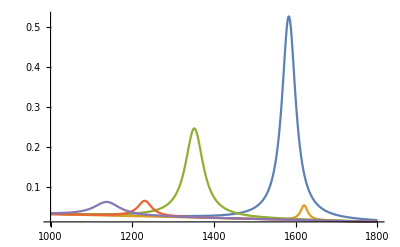

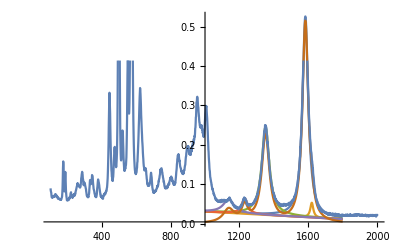

```mathematica
Plot[{fitOne,fitTwo,fitOneB,fitOneC,fitOneD},{x,1000,1800},PlotRange->All]
Show[{Plot[{fitOne,fitTwo,fitOneB,fitOneC,fitOneD,Total[{fitOne,fitTwo,fitOneB,fitOneC,fitOneD}-correction]},{x,1000,1800},PlotRange->All],ListLinePlot[graphite]}]
```

```mathematica
(*Should we include the linear background correction in the linewidth determination  - i SAY NO *)
```

```mathematica
FWHMone
```

40.7536

```mathematica
graphiteMaxPoints={{peakOneFreq,intensityOne},{peakTwoFreq,intensityTwo},{peakOneFreqB,intensityOneB},{peakOneFreqC,intensityOneC},{peakOneFreqD,intensityOneD}}
graphiteMaxPoints//TableForm
graphiteWidthPoints={{peakOneFreq,halfIntensityOne,FWHMone/2},{peakTwoFreq,halfIntensityTwo,FWHMtwo/2},{peakOneFreqB,halfIntensityOneB,FWHMoneB/2},{peakOneFreqC,halfIntensityOneC,FWHMoneC/2},{peakOneFreqD,halfIntensityOneD,FWHMoneD/2}};
graphiteWidthPoints//TableForm
```

{{1583.07,0.52558},{1620.51,0.0531712},{1351.81,0.245391},{1230.56,0.0643402},{1137.66,0.0615635}}

1583.07 | 0.52558
1620.51 | 0.0531712
1351.81 | 0.245391
1230.56 | 0.0643402
1137.66 | 0.0615635

1583.07 | 0.271185 | 20.3768
1620.51 | 0.0345258 | 10.5452
1351.81 | 0.133899 | 26.4852
1230.56 | 0.0448464 | 21.029
1137.66 | 0.0445862 | 38.7604

```mathematica
f/@graphiteWidthPoints
```

{f[{1583.07,0.271185,20.3768}],f[{1620.51,0.0345258,10.5452}],f[{1351.81,0.133899,26.4852}],f[{1230.56,0.0448464,21.029}],f[{1137.66,0.0445862,38.7604}]}

```mathematica
f2/@graphiteWidthPoints
```

{{{1583.07,0.254395},ErrorBar[20.3768,0]},{{1620.51,0.0186453},ErrorBar[10.5452,0]},{{1351.81,0.111492},ErrorBar[26.4852,0]},{{1230.56,0.0194938},ErrorBar[21.029,0]},{{1137.66,0.0169773},ErrorBar[38.7604,0]}}

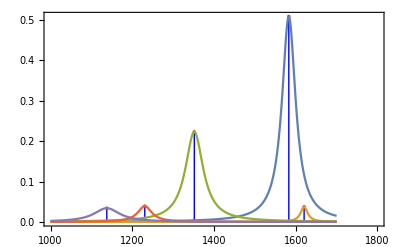

```mathematica
graphiteOnlyStates=Show[{ListPlot[f3/@graphiteMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->Directive[20,{PointSize[0.006],Red}],PlotRange->{{1000,1800},All}],Plot[{fitOne-correction,fitTwo-correction,fitOneB-correction,fitOneC-correction,fitOneD-correction},{x,1000,1700},PlotRange->{{1000,1800},All}]}]
```

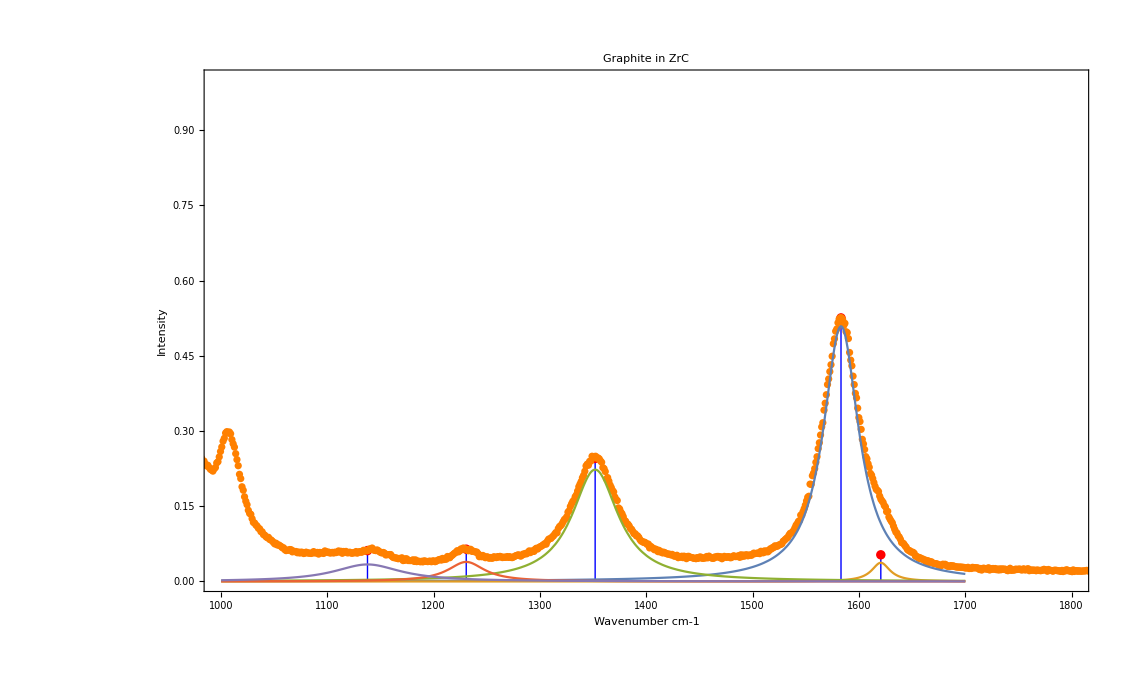

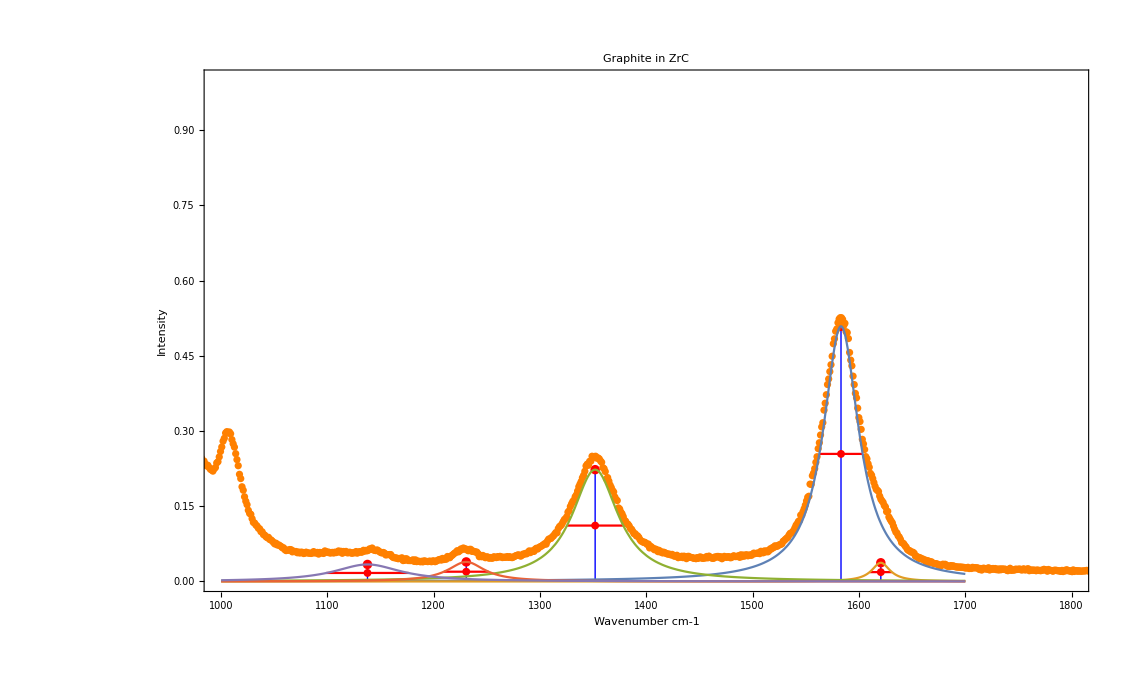

```mathematica
graphiteStates=Show[{ListPlot[graphiteMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{1000,1800},All}],ErrorListPlot[f/@graphiteWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{1000,1800},All}],Plot[{fitOne-correction,fitTwo-correction,fitOneB-correction,fitOneC-correction,fitOneD-correction},{x,1000,1700},PlotRange->{{1000,1800},All}]},PlotRange->{{1000,1800},All},PlotLabel->"Graphite in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
graphiteStates2=Show[{ListPlot[f3/@graphiteMaxPoints,Filling->Bottom,FillingStyle->Blue,Frame->True,PlotStyle->{PointSize[0.006],Red},PlotRange->{{1000,1800},All}],ErrorListPlot[f2/@graphiteWidthPoints,PlotStyle->{PointSize[0.005],Red}] ,ListPlot[graphite,PlotStyle->Orange,PlotRange->{{1000,1800},All}],Plot[{fitOne-correction,fitTwo-correction,fitOneB-correction,fitOneC-correction,fitOneD-correction},{x,1000,1700},PlotRange->{{1000,1800},All}]},PlotRange->{{1000,1800},All},PlotLabel->"Graphite in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

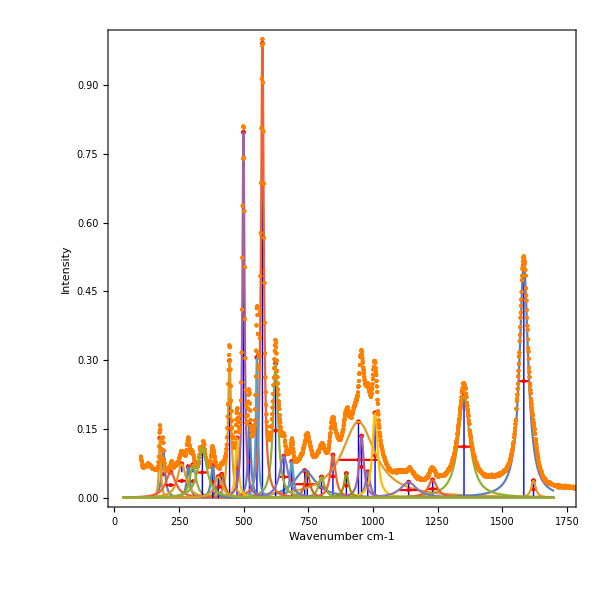

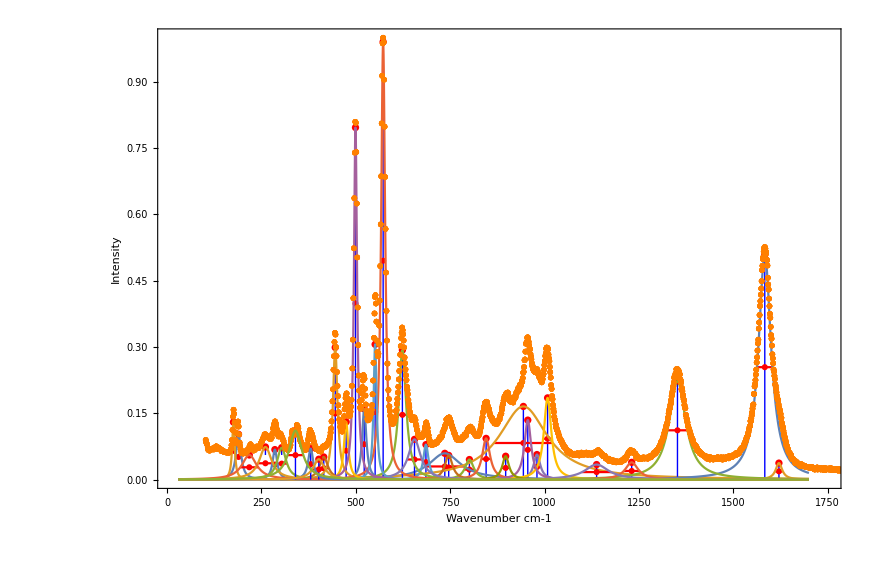

```mathematica
pRaman=Show[{defectStates,graphiteStates,carbonStates,zircStates,zircBStates,defectStatesB},PlotRange->{{10,1750},All}];
plotStates=Show[{defectStates2,graphiteStates2,carbonStates2,zircStates2,zircBStates2,defectStatesB2},PlotRange->{{10,1750},All},AspectRatio->1,ImageSize->{600,600},PlotLabel->"",LabelStyle->Directive[20,Black],FrameStyle->Directive[Thick,Black]]
plotStates66=Show[{defectStates2,graphiteStates2,carbonStates2,zircStates2,zircBStates2,defectStatesB2},PlotRange->{{10,1750},All},AspectRatio->0.66,ImageSize->{600,600},PlotLabel->"",LabelStyle->Directive[20,Black],FrameStyle->Directive[Thick,Black]]
```

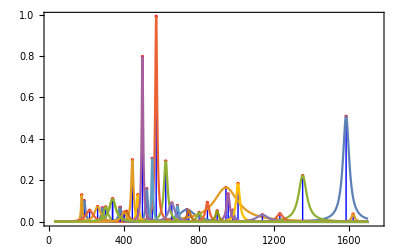

```mathematica
plotStatesOnly=Show[{defectOnlyStates2,defectOnlyStatesB2,graphiteOnlyStates,carbonOnlyStates2,zircOnlyStates2,zircOnlyBStates2,defectOnlyStatesB2},PlotRange->{{10,1750},All}]
```

```mathematica
"Graphite"
graphiteMaxPoints//TableForm
"High Defect states"
defectMaxPoints//TableForm
"Carbon states"
carbonMaxPoints//TableForm
"Low Defect states"
defectBMaxPoints//TableForm
"Zirconium"
zircBMaxPoints//TableForm
zircMaxPoints//TableForm

"Graphite"
graphiteWidthPoints//TableForm
"High Defect states"
defectWidthPoints//TableForm
"Carbon states"
carbonWidthPoints//TableForm
"Low Defect states"
defectBWidthPoints//Table
Form
"Zirconium"
zircBWidthPoints//TableForm
zircWidthPoints//TableForm
```

Graphite

1583.07 | 0.52558
1620.51 | 0.0531712
1351.81 | 0.245391
1230.56 | 0.0643402
1137.66 | 0.0615635

High Defect states

735.606 | 0.0967771
943.707 | 0.197857
800.764 | 0.081099
845.016 | 0.127918
979.682 | 0.0880362
745.905 | 0.0918739
685.645 | 0.117652
1007.84 | 0.215667
955.386 | 0.166615
896.802 | 0.086288

Carbon states

522.199 | 0.202487
445.422 | 0.343438
623.297 | 0.333215
572.301 | 1.03207
655.39 | 0.130325
415.044 | 0.0963371
551.087 | 0.347905
474.293 | 0.174321
499.096 | 0.839931

Low Defect states

380.45 | 0.115905
401.938 | 0.0915787
340.083 | 0.157647

Zirconium

285.592 | 0.116146
260.564 | 0.122681
303.63 | 0.120069
217.821 | 0.105582

189.27 | 0.153089
175.863 | 0.181093

Graphite

1583.07 | 0.271185 | 20.3768
1620.51 | 0.0345258 | 10.5452
1351.81 | 0.133899 | 26.4852
1230.56 | 0.0448464 | 21.029
1137.66 | 0.0445862 | 38.7604

High Defect states

735.606 | 0.067076 | 51.4896
943.707 | 0.115089 | 78.1516
800.764 | 0.0584456 | 13.9148
845.016 | 0.0813176 | 12.5126
979.682 | 0.0597413 | 10.6499
745.905 | 0.0644993 | 12.3552
685.645 | 0.07812 | 8.32988
1007.84 | 0.123215 | 11.9472
955.386 | 0.0993256 | 10.6185
896.802 | 0.0598737 | 10.7291

Carbon states

522.199 | 0.122523 | 6.80108
445.422 | 0.193931 | 7.26751
623.297 | 0.186659 | 11.8034
572.301 | 0.536707 | 6.45998
655.39 | 0.0848243 | 19.8231
415.044 | 0.0707493 | 13.5726
551.087 | 0.194881 | 4.87034
474.293 | 0.109022 | 6.85992
499.096 | 0.441525 | 4.99322

Low Defect states

{{380.45,0.0809533,8.20107},{401.938,0.0685293,17.8795},{340.083,0.102314,21.0349}}

Form

Zirconium

285.592 | 0.0822259 | 7.35919
260.564 | 0.0857972 | 19.9218
303.63 | 0.0839682 | 14.4777
217.821 | 0.0777672 | 23.9227

189.27 | 0.101867 | 7.92042
175.863 | 0.116032 | 4.1484

```mathematica
Transpose[%2183]
```

Transpose[%2183]

```mathematica
Sort[carbonWidthPoints,2]//TableForm
```

522.199 | 0.122523 | 6.80108
445.422 | 0.193931 | 7.26751
623.297 | 0.186659 | 11.8034
572.301 | 0.536707 | 6.45998
655.39 | 0.0848243 | 19.8231
415.044 | 0.0707493 | 13.5726
551.087 | 0.194881 | 4.87034
474.293 | 0.109022 | 6.85992
499.096 | 0.441525 | 4.99322

```mathematica
Transpose[carbonWidthPoints]//TableForm
```

522.199 | 445.422 | 623.297 | 572.301 | 655.39 | 415.044 | 551.087 | 474.293 | 499.096
0.122523 | 0.193931 | 0.186659 | 0.536707 | 0.0848243 | 0.0707493 | 0.194881 | 0.109022 | 0.441525
6.80108 | 7.26751 | 11.8034 | 6.45998 | 19.8231 | 13.5726 | 4.87034 | 6.85992 | 4.99322

```mathematica
g[x_]:=Transpose[{Transpose[x][[1]],Transpose[x][[2]]/Max@Transpose[x][[2]],Transpose[x][[3]]}]
```

```mathematica
SortBy[g[carbonWidthPoints],#[[1]]&]//TableForm
```

415.044 | 0.131821 | 13.5726
445.422 | 0.361334 | 7.26751
474.293 | 0.203131 | 6.85992
499.096 | 0.822656 | 4.99322
522.199 | 0.228286 | 6.80108
551.087 | 0.363104 | 4.87034
572.301 | 1. | 6.45998
623.297 | 0.347785 | 11.8034
655.39 | 0.158046 | 19.8231

```mathematica
SortBy[carbonWidthPoints,#[[2]]&]//TableForm
SortBy[carbonWidthPoints,#[[1]]&]//TableForm
```

415.044 | 0.0707493 | 13.5726
655.39 | 0.0848243 | 19.8231
474.293 | 0.109022 | 6.85992
522.199 | 0.122523 | 6.80108
623.297 | 0.186659 | 11.8034
445.422 | 0.193931 | 7.26751
551.087 | 0.194881 | 4.87034
499.096 | 0.441525 | 4.99322
572.301 | 0.536707 | 6.45998

415.044 | 0.0707493 | 13.5726
445.422 | 0.193931 | 7.26751
474.293 | 0.109022 | 6.85992
499.096 | 0.441525 | 4.99322
522.199 | 0.122523 | 6.80108
551.087 | 0.194881 | 4.87034
572.301 | 0.536707 | 6.45998
623.297 | 0.186659 | 11.8034
655.39 | 0.0848243 | 19.8231

### Convolution analysis

```mathematica
defectB
```

```mathematica
defectFreqs=Join[Transpose[defectMaxPoints][[1]],Transpose[defectBMaxPoints][[1]]]
carbonFreqs=Transpose[carbonMaxPoints][[1]]
zircFreqs=Join[Transpose[zircMaxPoints][[1]],Transpose[zircBMaxPoints][[1]]]
graphiteFreqs=Transpose[graphiteMaxPoints][[1]]
```

{735.606,943.707,800.764,845.016,979.682,745.905,685.645,1007.84,955.386,896.802,380.45,401.938,340.083}

{522.199,445.422,623.297,572.301,655.39,415.044,551.087,474.293,499.096}

{189.27,175.863,285.592,260.564,303.63,217.821}

{1583.07,1620.51,1351.81,1230.56,1137.66}

```mathematica
dStates=Transpose@{defectFreqs,Table[0.4,Length@defectFreqs]}
cStates=Transpose@{carbonFreqs,Table[0.5,Length@carbonFreqs]}
zrStates=Transpose@{zircFreqs,Table[0.5,Length@zircFreqs]}
gStates=Transpose@{graphiteFreqs,Table[0.5,Length@graphiteFreqs]}
cOuter2=Transpose@{DeleteDuplicates@Flatten@Outer[Plus,carbonFreqs,carbonFreqs],Table[0.6,Length@DeleteDuplicates@Flatten@Outer[Plus,carbonFreqs,carbonFreqs]]}
zrOuter2=Transpose@{DeleteDuplicates@Flatten@Outer[Plus,zircFreqs,zircFreqs],Table[0.6,Length@DeleteDuplicates@Flatten@Outer[Plus,zircFreqs,zircFreqs]]}
zrcOuter2=Transpose@{DeleteDuplicates@Flatten@Outer[Plus,zircFreqs,carbonFreqs],Table[0.7,Length@DeleteDuplicates@Flatten@Outer[Plus,zircFreqs,carbonFreqs]]}
```

{{735.606,0.4},{943.707,0.4},{800.764,0.4},{845.016,0.4},{979.682,0.4},{745.905,0.4},{685.645,0.4},{1007.84,0.4},{955.386,0.4},{896.802,0.4},{380.45,0.4},{401.938,0.4},{340.083,0.4}}

{{522.199,0.5},{445.422,0.5},{623.297,0.5},{572.301,0.5},{655.39,0.5},{415.044,0.5},{551.087,0.5},{474.293,0.5},{499.096,0.5}}

{{189.27,0.5},{175.863,0.5},{285.592,0.5},{260.564,0.5},{303.63,0.5},{217.821,0.5}}

{{1583.07,0.5},{1620.51,0.5},{1351.81,0.5},{1230.56,0.5},{1137.66,0.5}}

{{1044.4,0.6},{967.622,0.6},{1145.5,0.6},{1094.5,0.6},{1177.59,0.6},{937.243,0.6},{1073.29,0.6},{996.492,0.6},{1021.3,0.6},{890.845,0.6},{1068.72,0.6},{1017.72,0.6},{1100.81,0.6},{860.466,0.6},{996.509,0.6},{919.715,0.6},{944.518,0.6},{1246.59,0.6},{1195.6,0.6},{1278.69,0.6},{1038.34,0.6},{1174.38,0.6},{1097.59,0.6},{1122.39,0.6},{1144.6,0.6},{1227.69,0.6},{987.344,0.6},{1123.39,0.6},{1046.59,0.6},{1071.4,0.6},{1310.78,0.6},{1070.43,0.6},{1206.48,0.6},{1129.68,0.6},{1154.49,0.6},{830.088,0.6},{966.13,0.6},{889.336,0.6},{914.139,0.6},{1102.17,0.6},{1025.38,0.6},{1050.18,0.6},{948.585,0.6},{973.388,0.6},{998.191,0.6}}

{{378.54,0.6},{365.133,0.6},{474.862,0.6},{449.833,0.6},{492.9,0.6},{407.091,0.6},{351.726,0.6},{461.455,0.6},{436.426,0.6},{479.493,0.6},{393.684,0.6},{571.184,0.6},{546.156,0.6},{589.222,0.6},{503.413,0.6},{521.127,0.6},{564.194,0.6},{478.385,0.6},{607.26,0.6},{521.451,0.6},{435.642,0.6}}

{{711.469,0.7},{634.692,0.7},{812.567,0.7},{761.57,0.7},{844.66,0.7},{604.314,0.7},{740.356,0.7},{663.562,0.7},{688.365,0.7},{698.062,0.7},{621.285,0.7},{799.16,0.7},{748.163,0.7},{831.253,0.7},{590.907,0.7},{726.949,0.7},{650.155,0.7},{674.958,0.7},{807.792,0.7},{731.014,0.7},{908.889,0.7},{857.893,0.7},{940.982,0.7},{700.636,0.7},{836.679,0.7},{759.885,0.7},{784.688,0.7},{782.763,0.7},{705.986,0.7},{883.86,0.7},{832.864,0.7},{915.954,0.7},{675.607,0.7},{811.65,0.7},{734.856,0.7},{759.659,0.7},{825.829,0.7},{749.052,0.7},{926.927,0.7},{875.931,0.7},{959.02,0.7},{718.674,0.7},{854.717,0.7},{777.923,0.7},{802.726,0.7},{740.021,0.7},{663.243,0.7},{841.118,0.7},{790.122,0.7},{873.211,0.7},{632.865,0.7},{768.908,0.7},{692.114,0.7},{716.917,0.7}}

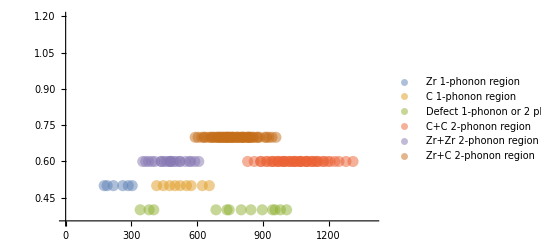

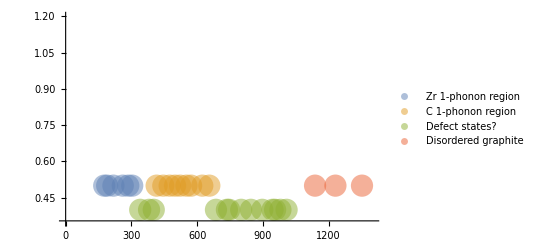

```mathematica
pJdos=ListPlot[{zrStates,cStates,dStates,cOuter2,zrOuter2,zrcOuter2},FillingStyle->Thickness[0.01],PlotStyle->Directive[PointSize[0.02],Opacity[0.5]]
,PlotRange->{{0,1400},{0.35,1.2}},PlotLegends->{"Zr 1-phonon region","C 1-phonon region","Defect 1-phonon or 2 phonon states?","C+C 2-phonon region","Zr+Zr 2-phonon region","Zr+C 2-phonon region"}]
pJdos2=ListPlot[{zrStates,cStates,dStates,gStates},FillingStyle->Thickness[0.01],PlotStyle->Directive[PointSize[0.04],Opacity[0.5]]
,PlotRange->{{0,1400},{0.35,1.2}},PlotLegends->{"Zr 1-phonon region","C 1-phonon region","Defect states?","Disordered graphite"}]
```

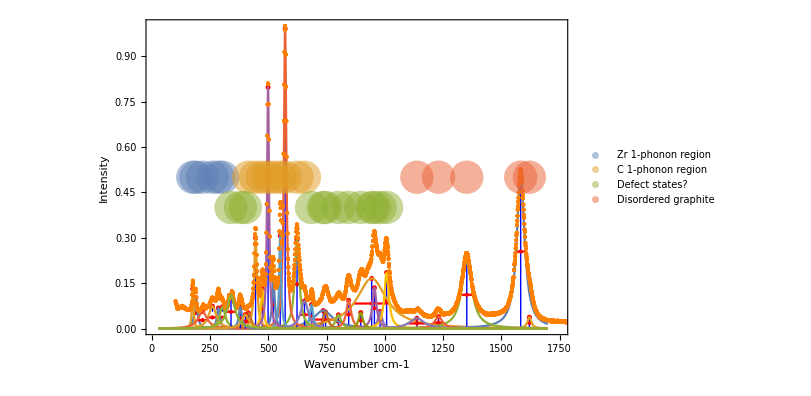

```mathematica
pRamanColouining=Show[{plotStates66,pJdos2}]
```

## Outer analysis

{{735.606,0.0967771},{943.707,0.197857},{800.764,0.081099},{845.016,0.127918},{979.682,0.0880362},{745.905,0.0918739},{685.645,0.117652},{1007.84,0.215667},{955.386,0.166615},{896.802,0.086288}}

{{522.199,0.202487},{445.422,0.343438},{623.297,0.333215},{572.301,1.03207},{655.39,0.130325},{415.044,0.0963371},{551.087,0.347905},{474.293,0.174321},{499.096,0.839931}}

{{189.27,0.153089},{175.863,0.181093},{285.592,0.116146},{260.564,0.122681},{303.63,0.120069},{217.821,0.105582},{522.199,0.202487},{445.422,0.343438},{623.297,0.333215},{572.301,1.03207},{655.39,0.130325},{415.044,0.0963371},{551.087,0.347905},{474.293,0.174321},{499.096,0.839931}}

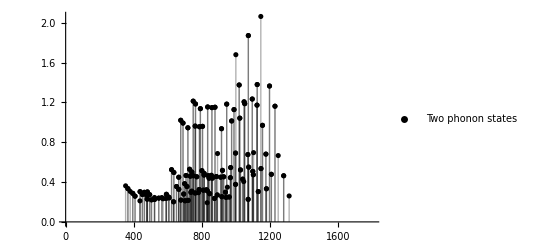

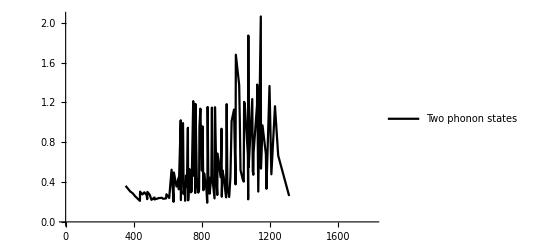

```mathematica
defectMaxPoints
carbonMaxPoints
jAllMaxPoints=Join[zircMaxPoints,zircBMaxPoints,carbonMaxPoints]
outer[{arg_,barg_}]:=Partition[Flatten@Table[Table[arg[[i]]+barg[[j]],{i,1,Length@arg}],{j,1,Length@barg}],2]


ListPlot[outer[{carbonMaxPoints,carbonMaxPoints}],Filling->Bottom];
ListPlot[outer[{jzircMaxPoints,jzircMaxPoints}],Filling->Bottom];
twoOuter=SortBy[outer[{jAllMaxPoints,jAllMaxPoints}],#[[1]]&];
pTwoStates=ListPlot[twoOuter,Filling->Bottom,PlotLegends->{"Two phonon states"},PlotStyle->Black,PlotRange->{{0,1800},All}]
pTwoStatesL=ListLinePlot[twoOuter,PlotLegends->{"Two phonon states"},PlotStyle->Black,PlotRange->{{0,1800},All}]
```

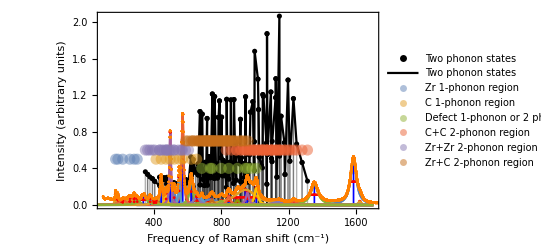

```mathematica
Show[{pTwoStates,pTwoStatesL,plotStates,pRamanColouining},PlotRange->{{100,1700},All},Frame->True,FrameLabel->{"Frequency of Raman shift (cm^-1)","Intensity (arbitrary units)"}]
```

### Select most important 1-phonon states

```mathematica
carbonMaxPointsTop4=Reverse[SortBy[carbonMaxPoints,#[[2]]&]][[1;;6]];
carbonMaxPointsTop4//TableForm
jzircMaxPoints=Join[zircMaxPoints,zircBMaxPoints];
zircMaxPointsTop4=Reverse[SortBy[jzircMaxPoints,#[[2]]&]][[1;;4]];
zircMaxPointsTop4//TableForm
```

572.301 | 1.03207
499.096 | 0.839931
551.087 | 0.347905
445.422 | 0.343438
623.297 | 0.333215
522.199 | 0.202487

175.863 | 0.181093
189.27 | 0.153089
260.564 | 0.122681
303.63 | 0.120069

```mathematica
zircMaxPointsTop4[[1]]
```

{175.863,0.181093}

```mathematica
{-zircMaxPointsTop4[[1]][[1]],zircMaxPointsTop4[[1]][[2]]}
```

{-175.863,0.181093}

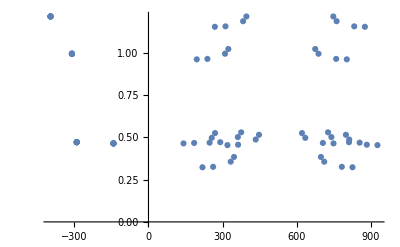

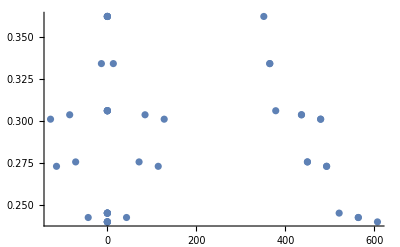

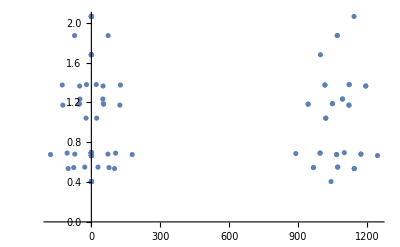

```mathematica
outerPM[{arg_,barg_}]:=Partition[Join[Flatten@Table[Table[arg[[i]]+barg[[j]],{i,1,Length@arg}],{j,1,Length@barg}],Flatten@Table[Table[arg[[i]]+{-barg[[j]][[1]],barg[[j]][[2]]},{i,1,Length@arg}],{j,1,Length@barg}],Flatten@Table[Table[{-arg[[j]][[1]],arg[[j]][[2]]}+{barg[[j]][[1]],barg[[j]][[2]]},{i,1,Length@arg}],{j,1,Length@barg}]],2]

ListPlot@SortBy[outerPM[{carbonMaxPointsTop4,zircMaxPointsTop4}],#[[1]]&]
ListPlot@SortBy[outerPM[{zircMaxPointsTop4,zircMaxPointsTop4}],#[[1]]&]
ListPlot@SortBy[outerPM[{carbonMaxPointsTop4,carbonMaxPointsTop4}],#[[1]]&]
```

{{175.863,0.181093},{189.27,0.153089},{260.564,0.122681},{303.63,0.120069},{572.301,1.03207},{499.096,0.839931},{551.087,0.347905},{445.422,0.343438},{623.297,0.333215},{522.199,0.202487}}

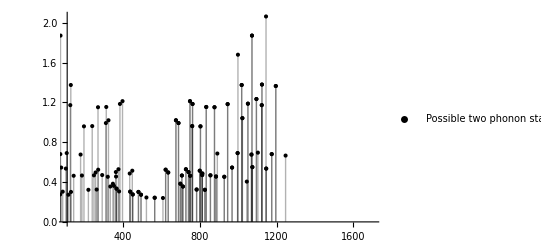

```mathematica
jointTopEight=Join[zircMaxPointsTop4,carbonMaxPointsTop4]
top2phononSumDiff=ListPlot[SortBy[outerPM[{jointTopEight,jointTopEight}],#[[1]]&],PlotRange->{{100,1700},All},Filling->Bottom,PlotStyle->Black,PlotLegends->{"Possible two phonon states: Zr+Zr, Zr+C, C+C, Zr-C, C-C, Zr-Zr"}]
```

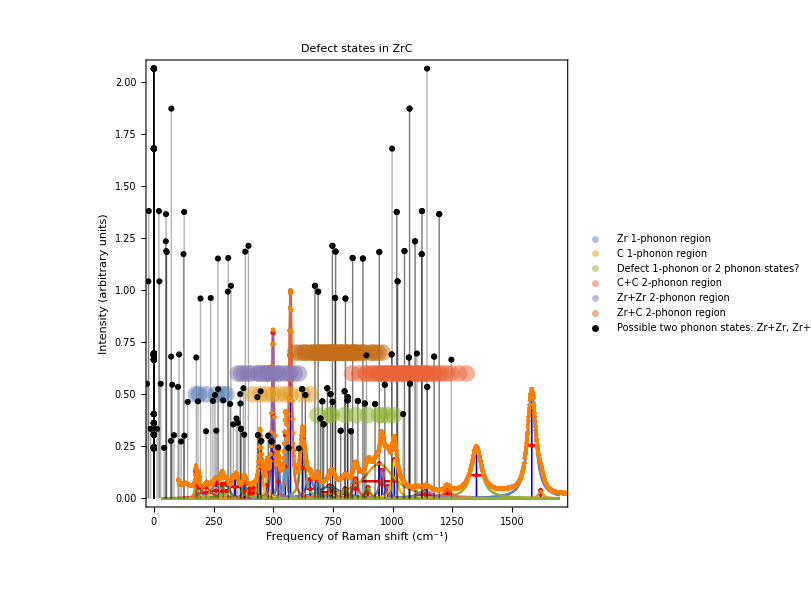

```mathematica
Show[{plotStates,pRamanColouining,top2phononSumDiff},PlotRange->{{1,1700},All},Frame->True,FrameLabel->{"Frequency of Raman shift (cm^-1)","Intensity (arbitrary units)"}]
```

```mathematica
jAllMaxPoints
```

{{189.27,0.153089},{175.863,0.181093},{285.592,0.116146},{260.564,0.122681},{303.63,0.120069},{217.821,0.105582},{522.199,0.202487},{445.422,0.343438},{623.297,0.333215},{572.301,1.03207},{655.39,0.130325},{415.044,0.0963371},{551.087,0.347905},{474.293,0.174321},{499.096,0.839931}}

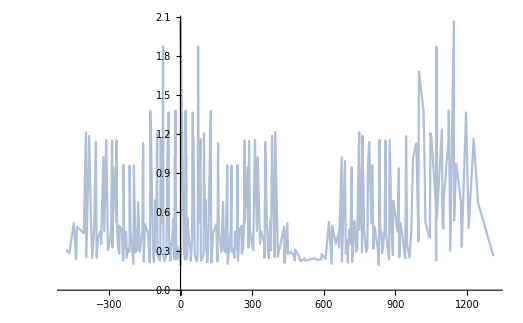

```mathematica
topAllphononSumDiff=ListLinePlot[SortBy[outerPM[{jAllMaxPoints,jAllMaxPoints}],#[[1]]&],PlotStyle->Opacity[0.5],PlotStyle->Blue]
```

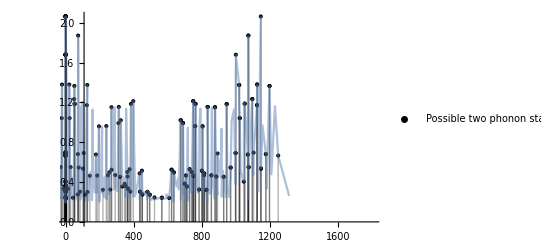

```mathematica
Show[{top2phononSumDiff,topAllphononSumDiff},PlotRange->{{0,1800},All}]
```

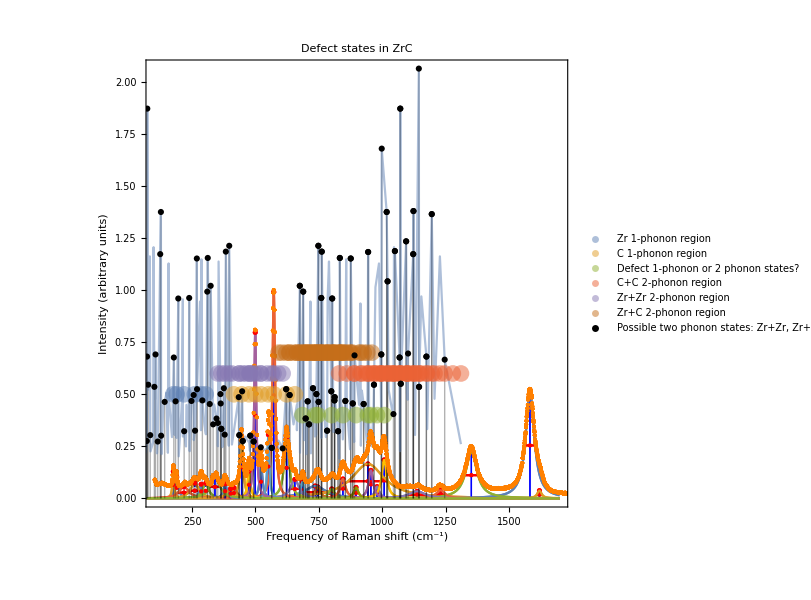

```mathematica
Show[{plotStates,pRamanColouining,Show[{top2phononSumDiff,topAllphononSumDiff},PlotRange->{{0,1800},All}]},PlotRange->{{100,1700},All},Frame->True,FrameLabel->{"Frequency of Raman shift (cm^-1)","Intensity (arbitrary units)"}]
```

## DFT peaks

```mathematica
thz2waavenum=1/0.0299792458;SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
phDOSfiles={"1.total_dos.dat","2.total_dos.dat","3.total_dos.dat","4.total_dos.dat","5.total_dos.dat","6.total_dos.dat","7.total_dos.dat","8.total_dos.dat","9.total_dos.dat","10.total_dos.dat","11.total_dos.dat"};
fren70dos=Table[ReadList[phDOSfiles[[i]],{Number,Number}],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/cvac_phon_dos"];
cvac=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/perf_phon_dos"];
perf=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-1126_phon_dos"];
fren1126=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-129_phon_dos"];
fren129=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-142_phon_dos"];
fren142=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-174_phon_dos"];
fren174=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
fren70=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
names2={"Perfet Zr32C32","CVAC Zr32C31 - 3 C at. %","Frenkel Zr32C32 -- Bound Dimer","Frenkel Zr32C32 -- Bound Trimer","Frenkel Zr32C32 -- Unbound Dimer","Frenkel Zr32C32 -- Unbound Trimer","Frenkel Zr32C32 -- Unbound Tetramer"};
(*names={"perf","fren129","fren142","fren70","fren174","fren1126","cvac"};
objects={perf,fren129,fren142,fren70,fren174,fren1126,cvac};*)
names={"cvac","fren129","fren142","fren70","fren174","fren1126"};
objects={cvac,fren129,fren142,fren70,fren174,fren1126};
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
fren1126Data=Table[Table[Flatten[{(fren1126[[j]][[i]][[1]]*thz2waavenum),vols[[j]],fren1126[[j]][[i]][[2]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
data=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,vols[[j]],objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
data2D=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

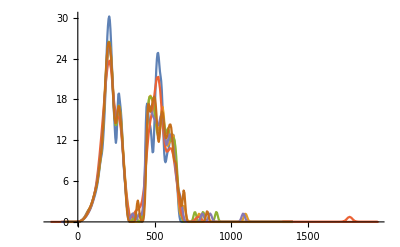

```mathematica
ListLinePlot@Table[data2D[[i]][[5]],{i,1,Length@data2D}]
```

```mathematica
data2Dint=Table[Table[Interpolation[data2D[[i]][[vol]]],{vol,1,Length@data2D[[1]]}],{i,1,Length@data2D}];
data2Dtab=Table[Table[Table[{x,data2Dint[[i]][[vol]][x]},{x,0,data2D[[i]][[vol]][[-1]][[1]],1}],{vol,1,Length@data2D[[1]]}],{i,1,Length@data2D}];
```

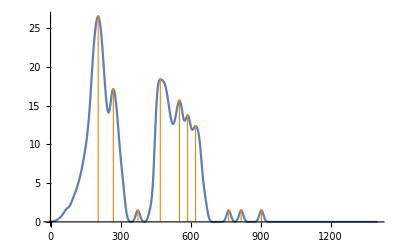

```mathematica
Show[{ListLinePlot[data2Dtab[[3]][[5]],PlotRange->All],ListPlot[data2Dtab[[3]][[5]] PeakDetect[Transpose[data2Dtab[[3]][[5]]][[2]],0,0,0.5],Filling->Bottom,FillingStyle->Thickness[0.002],PlotStyle->Directive[Orange]]}]
```

```mathematica
peaks=Table[Table[DeleteCases[data2Dtab[[type]][[vol]] PeakDetect[Transpose[data2Dtab[[type]][[vol]]][[2]],0,0,0.01],x_/;x[[1]]<0.1],{vol,1,9}],{type,1,5}];
peaks2=Table[Table[DeleteCases[data2Dtab[[type]][[vol]] PeakDetect[Transpose[data2Dtab[[type]][[vol]]][[2]],0,0,0.01],x_/;x[[1]]<0.1],{type,1,5}],{vol,1,9}];
```

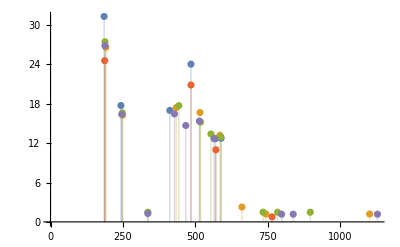

```mathematica
ListPlot[peaks2[[7]],Filling->Bottom]
```

```mathematica
peaksDefects=Table[Table[DeleteCases[DeleteCases[data2Dtab[[type]][[vol]] PeakDetect[Transpose[data2Dtab[[type]][[vol]]][[2]],9,0,0.1],x_/;x[[1]]<0.1],x_/;x[[2]]>6],{type,1,5}],{vol,1,11}];
```

Part::partw: Part 10 of {{{0,0.00501267},{1,0.00620928},{2,0.00762641},{3,0.00928334},{4,0.0111967},{5,0.013386},{6,0.0158773},{7,0.0186985},{8,0.0218439},{9,0.0253249},{10,0.0291532},{11,0.0333582},«27»,{39,0.310709},{40,0.326586},{41,0.342887},{42,0.359617},{43,0.376781},{44,0.394382},{45,0.412422},{46,0.430905},{47,0.449834},{48,0.469212},{49,0.489044},«1351»},{«1»},«5»,{«1»},{«1»}} does not exist.

Part::partw: Part 2 of Transpose[«1»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

PeakDetect::arg: The argument Transpose[{{{0,0.00501267},{1,0.00620928},{2,0.00762641},{3,0.00928334},{4,0.0111967},{5,0.013386},{6,0.0158773},{7,0.0186985},{8,0.0218439},{9,0.0253249},{10,0.0291532},{11,0.0333582},«27»,{39,0.310709},{40,0.326586},{41,0.342887},{42,0.359617},{43,0.376781},{44,0.394382},{45,0.412422},{46,0.430905},{47,0.449834},{48,0.469212},{49,0.489044},«1351»},«8»}⟦10⟧]⟦2⟧ at position 1 is not a consistent list of real values.

PeakDetect::arg: The argument Transpose[{{{0,0.0143127},{1,0.0165253},{2,0.0189954},{3,0.0217495},{4,0.024795},{5,0.0281457},{6,0.031817},{7,0.0358241},{8,0.0401825},{9,0.0449192},{10,0.0500596},{11,0.0555905},«27»,{39,0.399956},{40,0.419761},{41,0.440147},{42,0.461105},{43,0.482654},{44,0.504814},{45,0.527598},{46,0.551018},{47,0.575085},{48,0.599813},{49,0.625222},«1351»},«7»,{«1»}}⟦10⟧]⟦2⟧ at position 1 is not a consistent list of real values.

PeakDetect::arg: The argument Transpose[{{{0,0.0100279},{1,0.0118403},{2,0.0139},{3,0.0162319},{4,0.0188449},{5,0.0217558},{6,0.0249815},{7,0.0285389},{8,0.0324594},{9,0.0367575},{10,0.0414294},{11,0.0464861},«27»,{39,0.372726},{40,0.391629},{41,0.411099},{42,0.43112},{43,0.451716},{44,0.472919},{45,0.494747},{46,0.517218},{47,0.540348},{48,0.564109},{49,0.588572},«1351»},«7»,{«1»}}⟦10⟧]⟦2⟧ at position 1 is not a consistent list of real values.

General::stop: Further output of PeakDetect::arg will be suppressed during this calculation.

```mathematica
peaksDefects//Dimensions
ListPlot[peaksDefects[[5]],Filling->Bottom,PlotRange->{{0,1100},{0,5}}]
```

{11,5}

ListPlot::lpn: {{},{{691.,2.34537},{791.,1.20928},{1092.,1.21037}},{{374.,1.46305},{763.,1.46189},{816.,1.4634},{903.,1.46352}},{{784.,0.744534}},{{357.,1.231},{811.,1.23081},{862.,1.23344},{1077.,1.22583}}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{},{{691,2.34537},{791,1.20928},{1092,1.21037}},{{374,1.46305},{763,1.46189},{816,1.4634},{903,1.46352}},{{784,0.744534}},{{357,1.231},{811,1.23081},{862,1.23344},{1077,1.22583}}},Filling→Bottom,PlotRange→{{0,1100},{0,5}}]

Transpose::nmtx: The first two levels of {} cannot be transposed.

{{},{691,791,1092},{374,763,816,903},{784},{357,811,862,1077}}

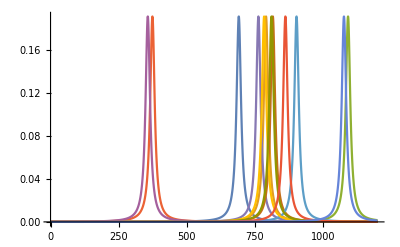

```mathematica
defectFreqs=Table[Transpose[peaksDefects[[5]][[i]]][[1]],{i,1,5}]
defectLorentz=With[{a=10},Table[Table[3a/5*PDF[CauchyDistribution[defectFreqs[[j]][[i]],a],x],{i,1,defectFreqs[[j]]//Length}],{j,1,Length@defectFreqs}]];
dftDefectP=Plot[defectLorentz,{x,0,1200},PlotRange->All]
```

-Graphics-

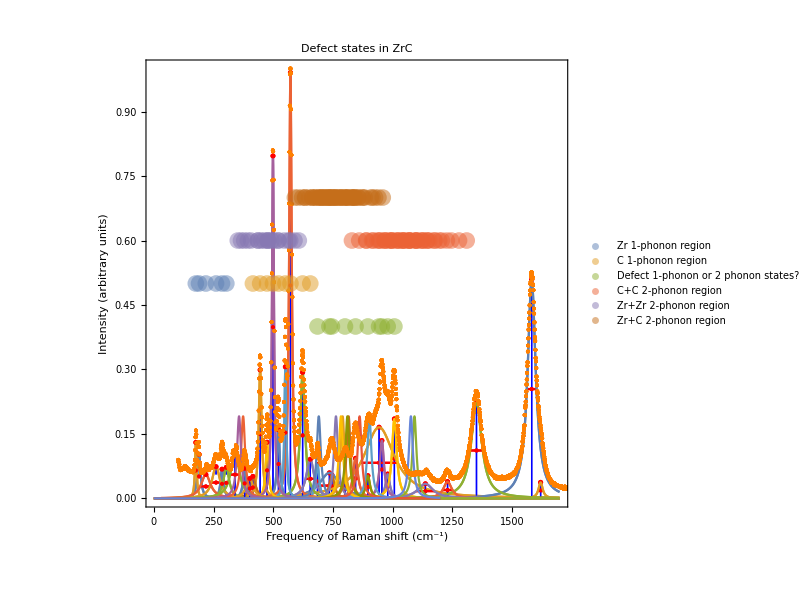

```mathematica
dftDefectP
Show[{plotStates,pRamanColouining,dftDefectP},PlotRange->{{1,1700},All},Frame->True,FrameLabel->{"Frequency of Raman shift (cm^-1)","Intensity (arbitrary units)"}]
```

```mathematica
GraphicsGrid@{{gridDefects},{plotStates}};
```

```mathematica
{p1,p2,p3,p4,p5}=Table[Plot[defectLorentz[[i]],{x,0,1750},FrameTicks->{Automatic,None},Frame->True,ImageSize->600,AspectRatio->0.1,PlotRange->{{500,1100},All},PlotStyle->Directive[Thickness[0.06]]],{i,1,5}];
```

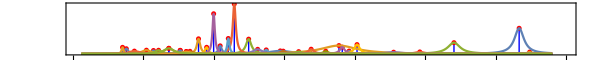

```mathematica
plotStatesOnly=Show[{defectOnlyStates2,defectOnlyStatesB2,graphiteOnlyStates,carbonOnlyStates2,zircOnlyStates2,zircOnlyBStates2,defectOnlyStatesB2},PlotRange->{{10,1750},All},AspectRatio->0.1,ImageSize->600,FrameTicks->{Automatic,None}]
```

```mathematica
p1
```

-Graphics-

```mathematica
gridDefects=GraphicsGrid[{{p1},{p2},{p3},{p4},{p5}},Spacings->-35,AspectRatio->1,ImageSize->{600,600}];
```

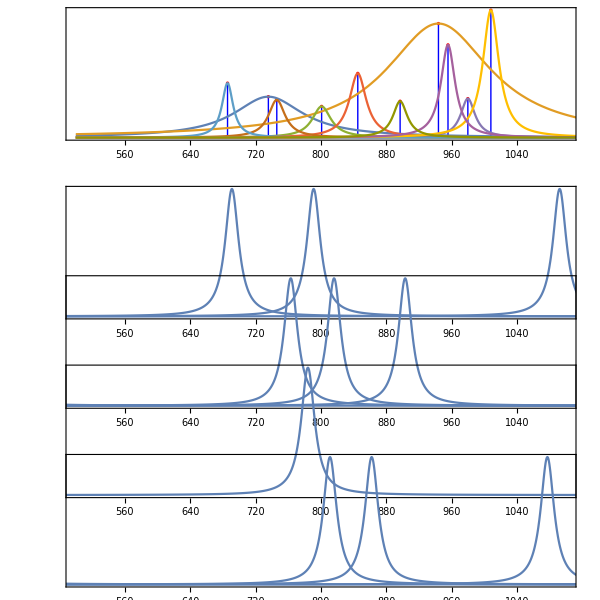

```mathematica
GraphicsGrid[{{Show[{defectOnlyStates2},FrameTicks->{Automatic,None},AspectRatio->0.1,PlotRange->{{500,1100},All}]},{p1},{p2},{p3},{p4},{p5}},Spacings->-25,AspectRatio->0.5,ImageSize->{600,600}]
```

```mathematica
data2D//Dimensions
```

{6}

```mathematica
names2[[2;;-1]]
```

{CVAC Zr32C31 - 3 C at. %,Frenkel Zr32C32 -- Bound Dimer,Frenkel Zr32C32 -- Bound Trimer,Frenkel Zr32C32 -- Unbound Dimer,Frenkel Zr32C32 -- Unbound Trimer,Frenkel Zr32C32 -- Unbound Tetramer}

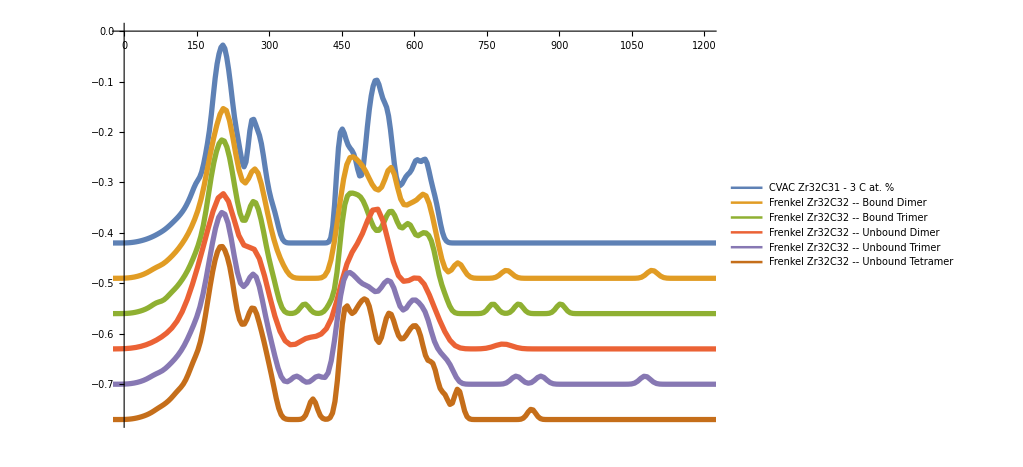

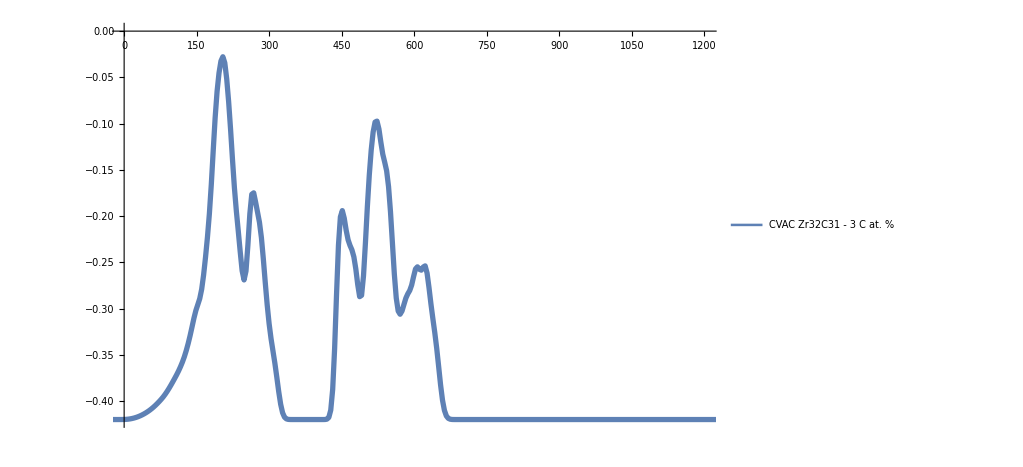

```mathematica
dosSeparated=ListLinePlot[Table[Transpose[{Transpose[data2D[[i]][[5]]][[1]],Transpose[data2D[[i]][[5]]][[2]]*0.013}]-0.35-i*0.07,{i,1,Length@data2D}],PlotLegends->Placed[Table[names2[[2;;-1]][[i]],{i,1,6}],{0.8,0.31}],PlotStyle->Thickness[0.005],PlotRange->{{0,1200},All}]
dosSeparated2=ListLinePlot[Table[Transpose[{Transpose[data2D[[i]][[5]]][[1]],Transpose[data2D[[i]][[5]]][[2]]*0.013}]-0.35-i*0.07,{i,1,1}],PlotStyle->Thickness[0.005],PlotLegends->Placed[Table[names2[[2;;-1]][[i]],{i,1,1}],{0.8,0.31}],PlotRange->{{0,1200},All}]
```

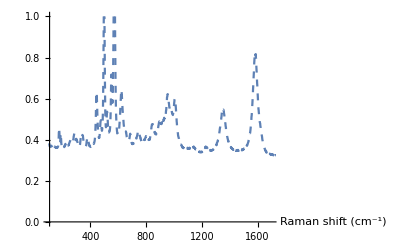

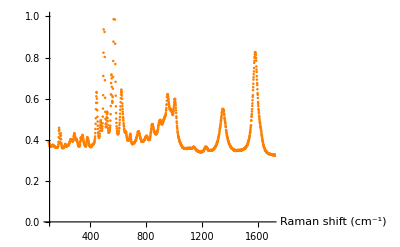

```mathematica
expRamanPlot=Show[{ListLinePlot[Transpose[{Transpose[expRaman][[1]],1*Transpose[expRaman][[3]]+0.3}],PlotRange->{{100,1700},{0,1}},PlotStyle->Dashed,AxesLabel->{Style["Raman shift (cm^-1)",18,Black],None}]}]
expRamanPlot3=Show[{ListPlot[Transpose[{Transpose[expRaman][[1]],1*Transpose[expRaman][[3]]+0.3}],PlotRange->{{100,1700},{0,1}},PlotStyle->Orange,AxesLabel->{Style["Raman shift (cm^-1)",18,Black],None}]}]
```

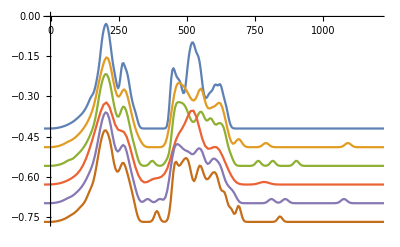

```mathematica
dosSeparated[[1]]
```

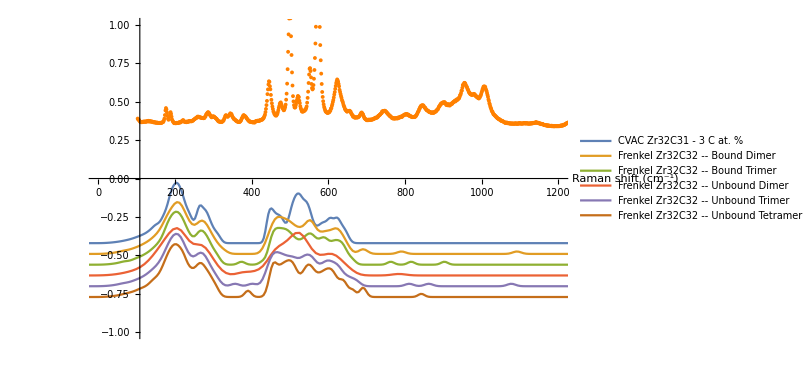

```mathematica
Show[{expRamanPlot3,dosSeparated},PlotRange->{{0,1200},{-1,1}}]
```

```mathematica
plotStatesOnly2=Show[{Show[{defectOnlyStates2,defectOnlyStatesB2,graphiteOnlyStates,carbonOnlyStates2,zircOnlyStates2,zircOnlyBStates2,defectOnlyStatesB2},PlotRange->{{10,1850},All},AspectRatio->0.75,ImageSize->600,FrameTicks->{Automatic,None},PlotStyle->Directive[Thickness[0.01]]],Show[{dosSeparated,expRamanPlot3}]},ImageSize->900,LabelStyle->Directive[18,Black],FrameStyle->Directive[Thick,Black],FrameLabel->{Style["Raman shift (cm^-1)",18,Black]}]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

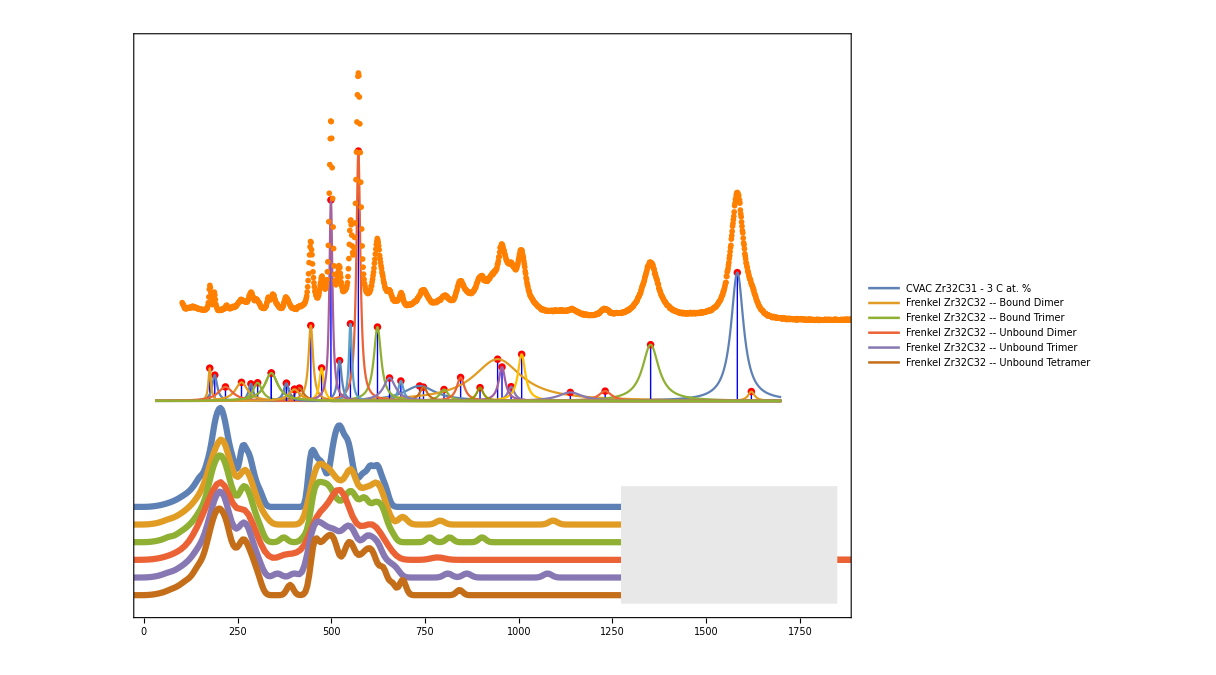

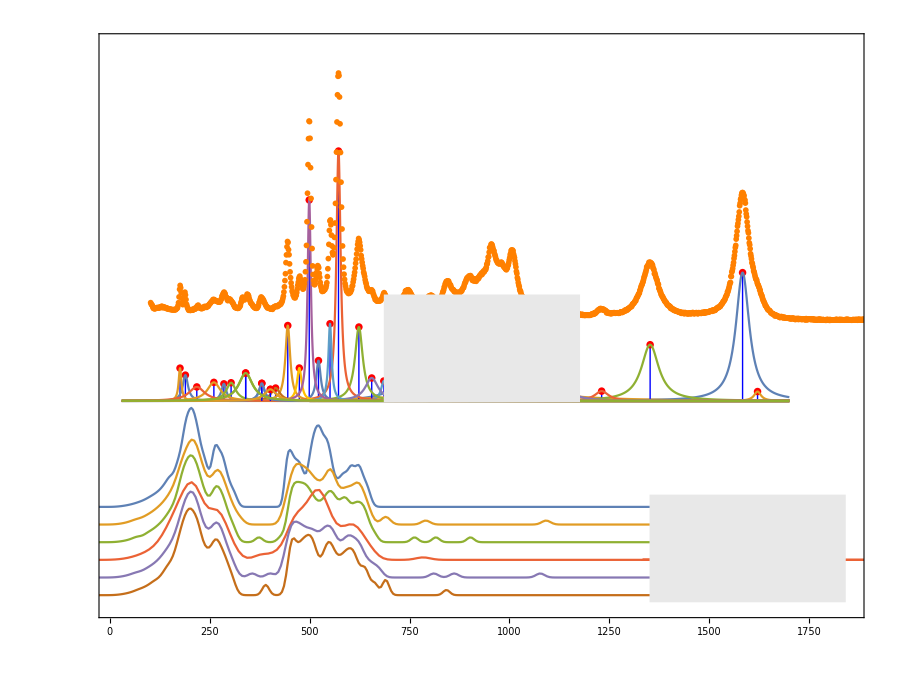

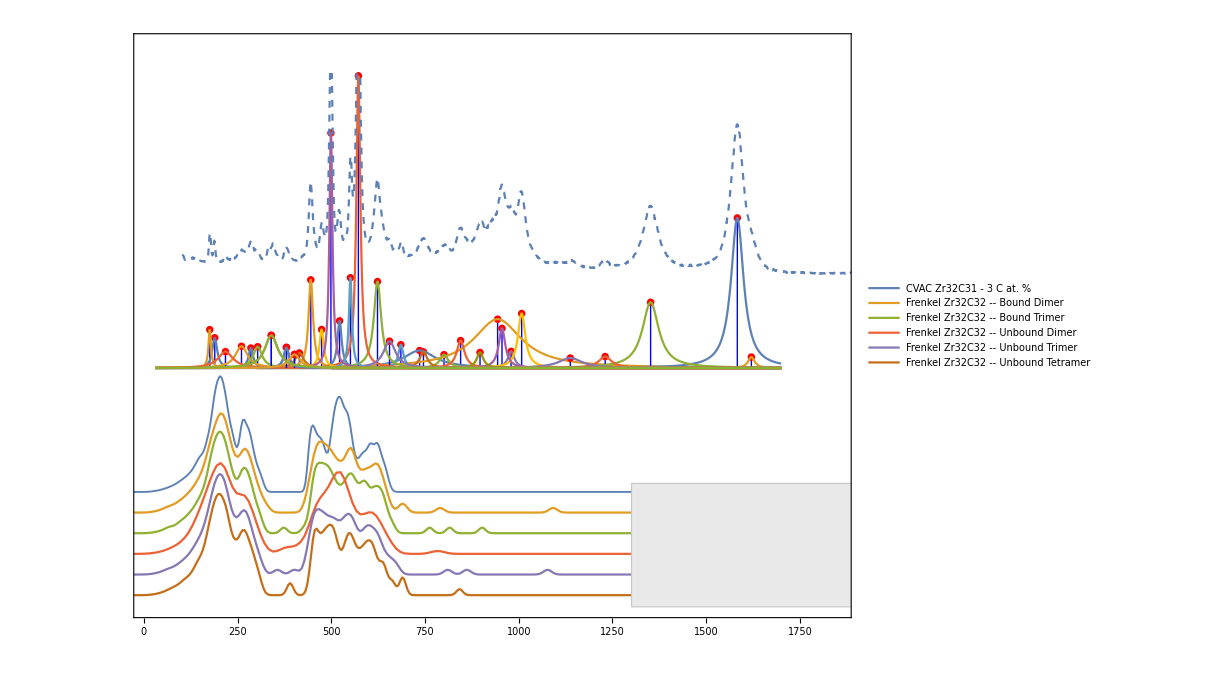

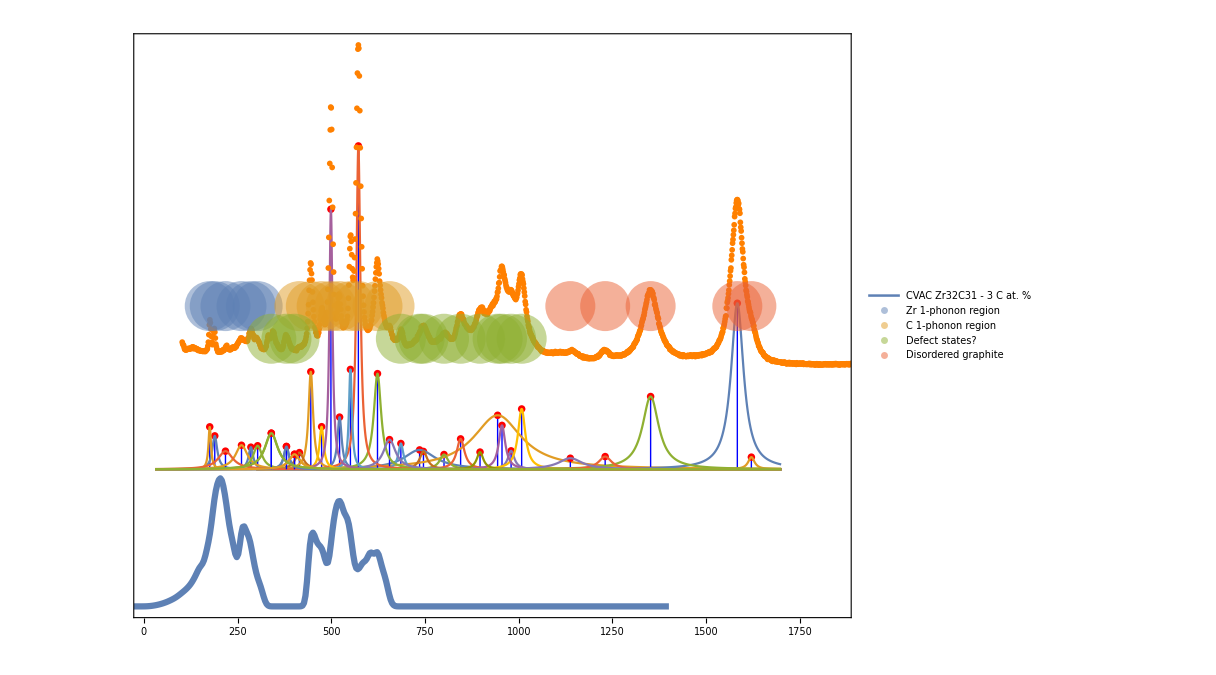

```mathematica
plotStatesOnly3=Show[{Show[{defectOnlyStates2,defectOnlyStatesB2,graphiteOnlyStates,carbonOnlyStates2,zircOnlyStates2,zircOnlyBStates2,defectOnlyStatesB2},PlotRange->{{10,1850},All},AspectRatio->0.75,ImageSize->600,FrameTicks->{Automatic,None}],Show[{dosSeparated2,expRamanPlot3,pJdos2}]},ImageSize->900,LabelStyle->Directive[18,Black],FrameStyle->Directive[Thick,Black],FrameLabel->{Style["Raman shift (cm^-1)",18,Black]}]
```

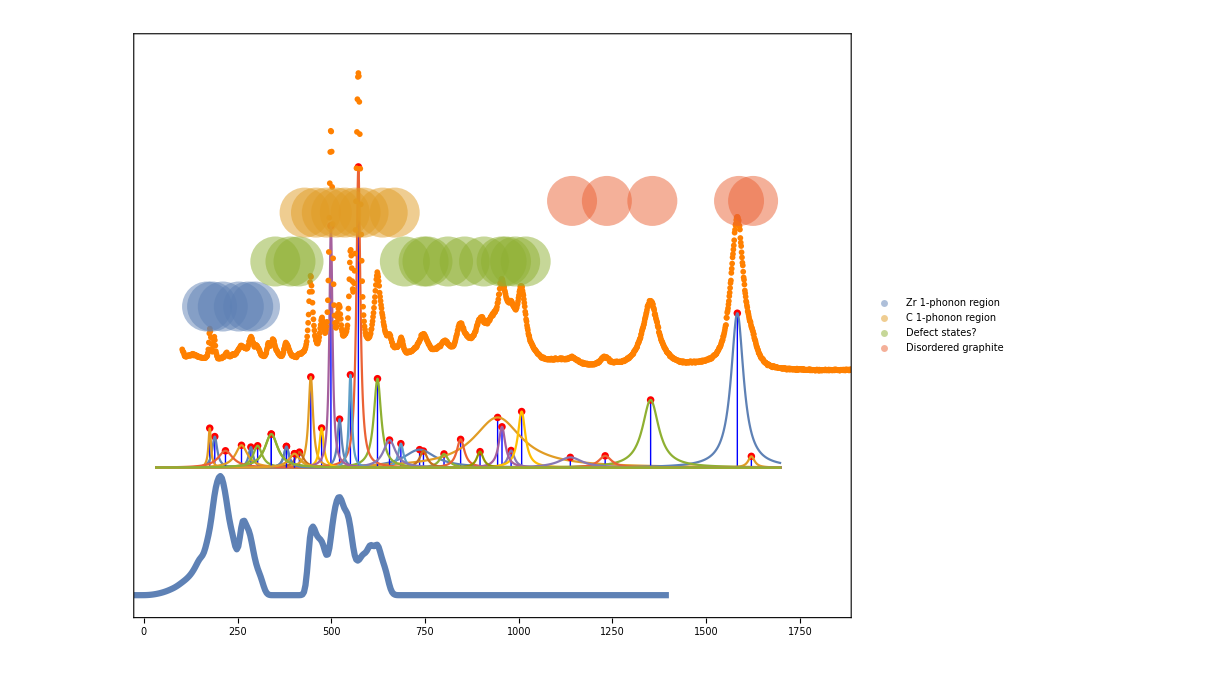

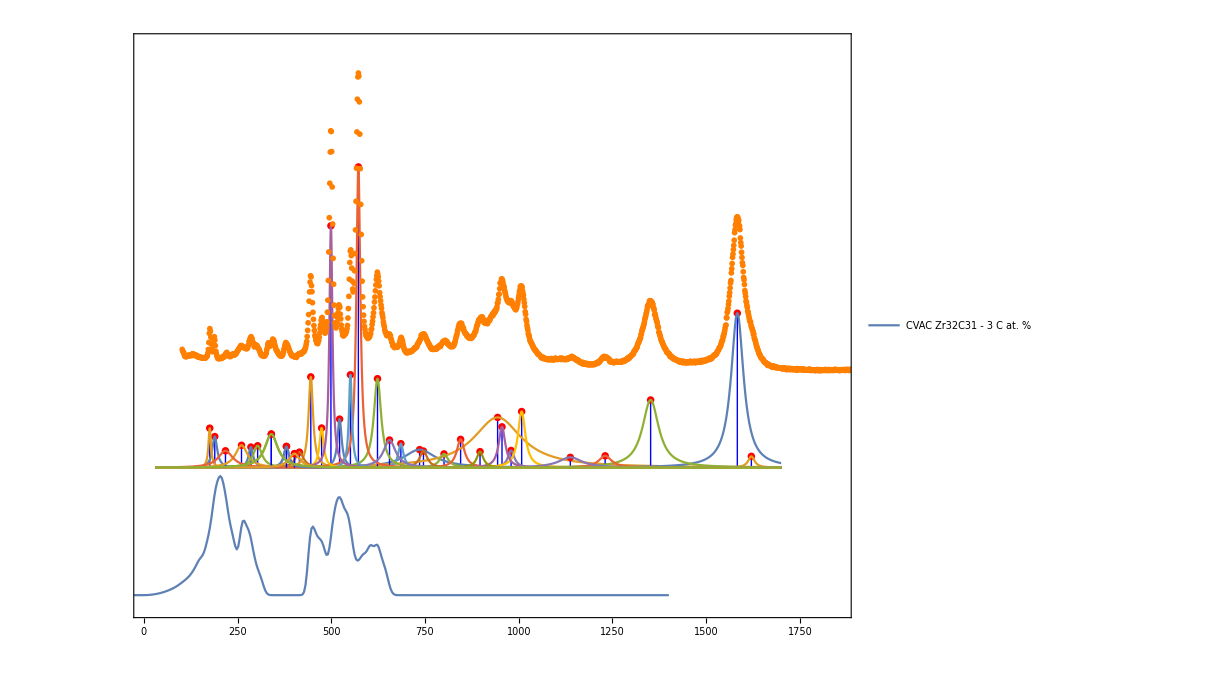

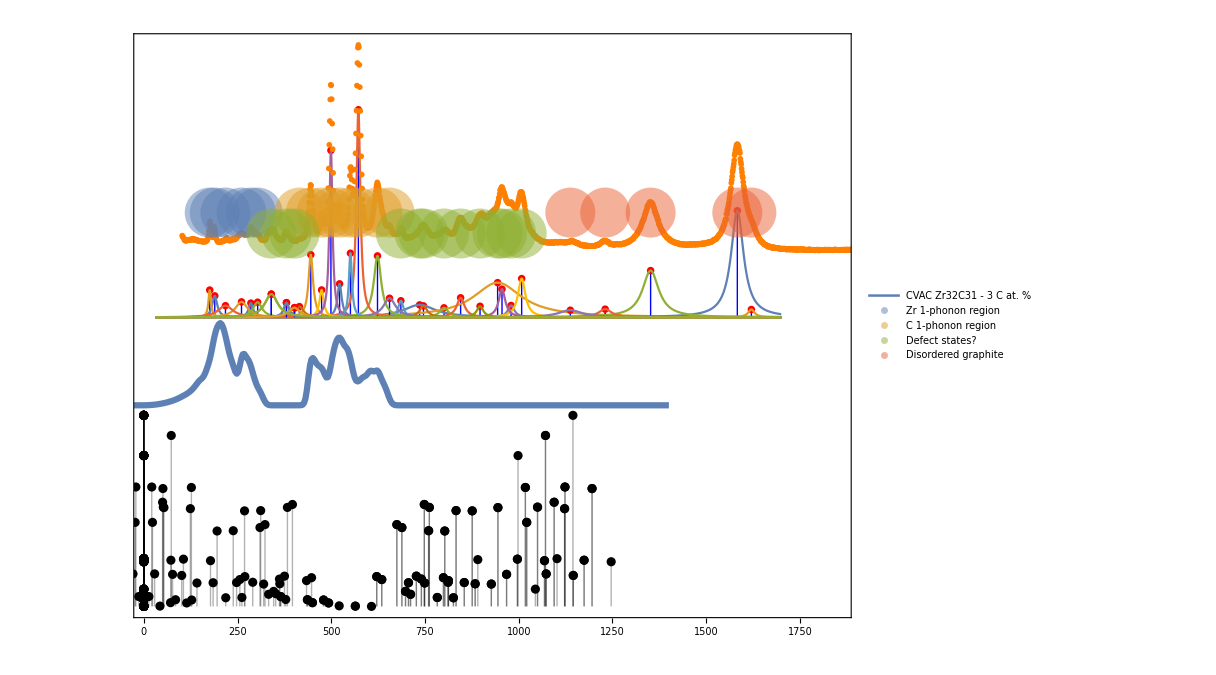

```mathematica
Show[{Show[{defectOnlyStates2,defectOnlyStatesB2,graphiteOnlyStates,carbonOnlyStates2,zircOnlyStates2,zircOnlyBStates2,defectOnlyStatesB2},PlotRange->{{10,1850},All},AspectRatio->0.75,ImageSize->600,FrameTicks->{Automatic,None}],Show[{dosSeparated2,expRamanPlot3,pJdos2,twoPhononStates}]},ImageSize->900,LabelStyle->Directive[18,Black],FrameStyle->Directive[Thick,Black],FrameLabel->{Style["Raman shift (cm^-1)",18,Black]}]
```

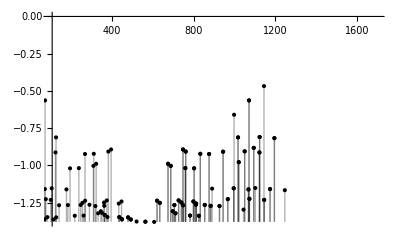

```mathematica
twoPhononStates=ListPlot[Transpose[{Transpose[SortBy[outerPM[{jointTopEight,jointTopEight}],#[[1]]&]][[1]],Transpose[SortBy[outerPM[{jointTopEight,jointTopEight}],#[[1]]&]][[2]]*0.5-1.5}],PlotRange->{{100,1700},All},Filling->Bottom,PlotStyle->Black]
```

### Fraction of Frenkel pairs for different recombination barriers

0.0000833333

192.143

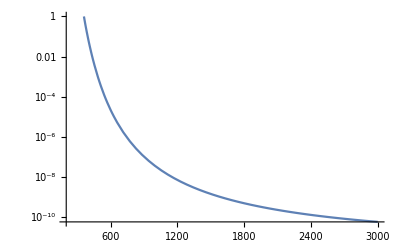

```mathematica
(*0.8, 0.7 and 0.6 eV barriers in years at 300K*)
t1[T_]:=(1/(10^12*Exp[-0.8/((0.025/300)*T)]//N))/3600*24*365
t2[T_]:=(1/(10^12*Exp[-0.7/(0.025/300)*T]//N))/3600*24*365
t3[T_]:=(1/(10^12*Exp[(-0.6/(0.025/300))*T]//N))/3600*24*365
t1[300]

LogPlot[t1[x],{x,200,3000}]
```

### Unbound pair recombination energy

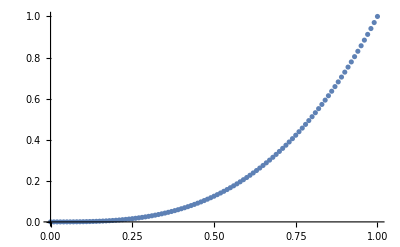

0.501001

```mathematica
ListPlot@Table[{r,r^3},{r,0,1,0.01}]
Total@Table[0.001*Abs@r^3,{r,-1,1,0.001}]
(*The expected distance of a particlar from a points in a cubic grid is 0.8*cube edge*)
(*The size of the cube is 1/conc - so the size of a cube edge conc^-0.333*)
```

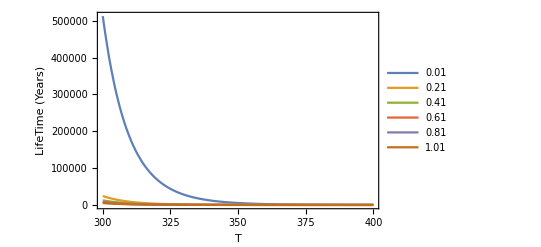

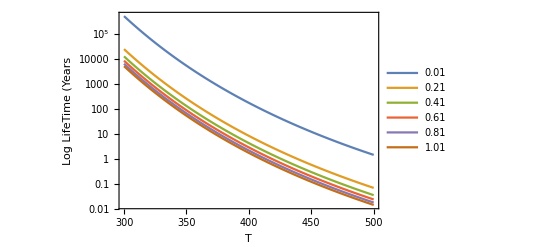

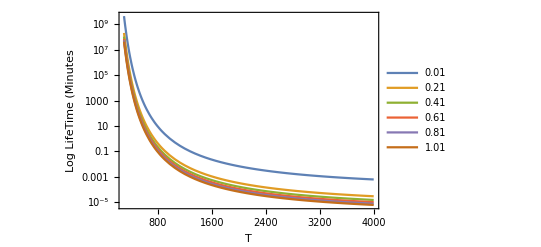

```mathematica
(*Defect lifetime = 1/(successProbability*AttemptFreq) times number of jumps expected to be required to recombination
number of jumps expected to be required for recombination is 0.8/conc
 *)

ub1[T_,conc_]:=((1/(10^12*Exp[-0.8/((0.025/300)*T)]//N))/3600*24*365)*0.8*(conc^-1/3)
Plot[Evaluate@Table[ub1[x,i/10000],{i,1,120,20}],{x,300,400},Frame->True,PlotLegends->Table[100*i/10000//N,{i,1,120,20}],FrameLabel->{"T","LifeTime (Years)"},PlotRange->All]
LogPlot[Evaluate@Table[ub1[x,i/10000],{i,1,120,20}],{x,300,500},Frame->True,PlotLegends->Table[100*i/10000//N,{i,1,120,20}],FrameLabel->{"T","Log LifeTime (Years"},PlotRange->All]
LogPlot[Evaluate@Table[ub1[x,i/10000]*24*365,{i,1,120,20}],{x,300,4000},Frame->True,PlotLegends->Table[100*i/10000//N,{i,1,120,20}],FrameLabel->{"T","Log LifeTime (Minutes"},PlotRange->All]
```

```mathematica
Exp[-10]^-1
```

ⅇ^10

```mathematica
f[x_]:=(1/(Exp[-1/x]))^3
f[w]
D[f[w],w]
```

ⅇ^(3/w)

-(3 ⅇ^(3/w))/w^2

```mathematica
(*Energy density
Megajoules per litre = eV/cubic angstrom times joules * angstrom per cubic metre*)
zrc3000perL=(((4.4/(9.8*9.8*9.8))*(1.6*10^-19)*10^30)/1000)/(10^6);
zrc50PercentperL=(((4.4/(2.4^3))*(1.6*10^-19)*10^30)/1000)/(10^6);
(*Specific energy
Megajoules per kilogram = eV/cubic angstrom times joules * angstrom per cubic metre*)
zrc3000perkG=(((((4.4/(9.8*9.8*9.8))*(1.6*10^-19)*10^30))/1000)/(10^6)/6);
zrc50PercentperkG=(((((4.4/(2.4^3))*(1.6*10^-19)*10^30))/1000)/(10^6)/6);
(*Energy density of petrol, supercapaictor, and lithium air-batteries*)
petrolPerKG=45;
petrolPerL=45;
tantPerKG=5;

coalPerKG=26;
coalPerL=34;

woodPerKG=16;
woodPerL=13;

lithiumBatteryPerKG=2;
lithiumBatteryPerL=4;
```

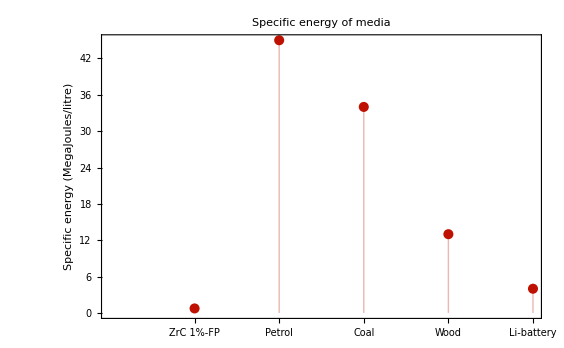

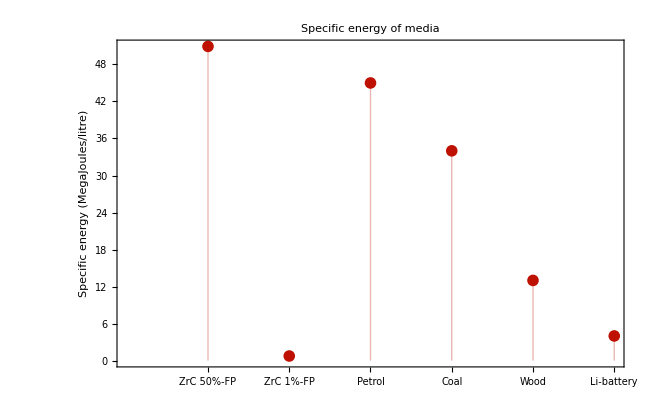

```mathematica
ListPlot[{zrc3000perL,petrolPerL,coalPerL,woodPerL,lithiumBatteryPerL},Filling->Bottom,Frame->True,FrameStyle->Thick,PlotStyle->20,FrameStyle->Directive[14],FrameTicksStyle->Directive[20,Black],PlotLabel->Style["Specific energy of media",20,Black],FrameTicks->{{Automatic,None},{{{1,Style["  ZrC 1%-FP",18,Black]},{2,Style["Petrol",18,Black]},{3,Style["Coal",18,Black]},{4,Style["Wood",18,Black]},{5,Style["Li-battery",18,Black]}},{None}}},FrameLabel->{Style["",18,Black],Style["Specific energy (MegaJoules/litre)",18,Black]}]

ListPlot[{zrc50PercentperL,zrc3000perL,petrolPerL,coalPerL,woodPerL,lithiumBatteryPerL},Filling->Bottom,Frame->True,FrameStyle->Thick,PlotStyle->20,FrameStyle->Directive[14],FrameTicksStyle->Directive[20,Black],PlotLabel->Style["Specific energy of media",20,Black],FrameTicks->{{Automatic,None},{{{1,Style["ZrC 50%-FP         ",18,Black]},{2,Style["      ZrC 1%-FP",18,Black]},{3,Style["Petrol",18,Black]},{4,Style["Coal",18,Black]},{5,Style["Wood",18,Black]},{6,Style["Li-battery",18,Black]}},{None}}},FrameLabel->{Style["",18,Black],Style["Specific energy (MegaJoules/litre)",18,Black]}]
```

```mathematica
ListPlot[{zrc50PercentperkG,zrc3000perkG,petrolPerKG,coalPerKG,woodPerKG,lithiumBatteryPerKG},Filling->Bottom,Frame->True,FrameStyle->Thick,PlotStyle->20,FrameStyle->Directive[14],FrameTicksStyle->Directive[20,Black],PlotLabel->Style["Energy density of media",20,Black],FrameTicks->{{Automatic,None},{{{1,Style["ZrC 50%-C amorphous         ",18,Black]},{2,Style["      Zr18,Black]},{3,Style["Petrol",18,Black]},{4,Style["Coal",18,Black]},{5,Style["Wood",18,Black]},{6,Style["Li-battery",18,Black]}},{None}}},FrameLabel→{Style["",18,Black],Style["Energy/kg",18,Black]}
```